C:\Users\Lpp\Desktop\data-drivenpipe\code_pipe

M matrix =

(0.0903797 | 0. | 0.
0. | 0.0903797 | 0.
0. | 0. | 0.0903797)

Kbend matrix (U-independent) =

(1693.71 | 0. | 0.
0. | 27099.3 | 0.
0. | 0. | 137190.)

KaxInt matrix (U factor separated) =

(4.9348 | 7.69468×10^-16 | -1.1542×10^-15
7.69468×10^-16 | 19.7392 | 2.3084×10^-15
-1.1542×10^-15 | 2.3084×10^-15 | 44.4132)

Frequencies at U = 0 m/s (Hz): {21.7873,87.1493,196.086}

Part::partw: {75.2845,184.698} 的部分 3 不存在.

Part::partw: {74.58,184.054} 的部分 3 不存在.

Part::partw: {73.8497,183.39} 的部分 3 不存在.

General::stop: 在本次计算中，Part::partw 的进一步输出将被抑制.

Part::partw: {75.2845,184.698} 的部分 3 不存在.

Part::partw: {74.58,184.054} 的部分 3 不存在.

Part::partw: {73.8497,183.39} 的部分 3 不存在.

General::stop: 在本次计算中，Part::partw 的进一步输出将被抑制.

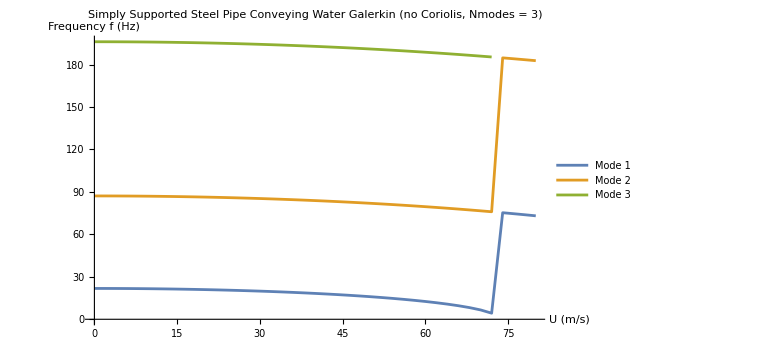

0 | 21.7873 | 87.1493 | 196.086
20 | 20.9641 | 86.3379 | 195.277
40 | 18.2732 | 83.8564 | 192.828
60 | 12.5673 | 79.5488 | 188.677
73.5 | 75.4567 | 184.856 |

```mathematica
SetDirectory@NotebookDirectory[]
(* ==================================*)(*Simply Supported Steel Pipe*)(*Conveying Water (Galerkin,no G)*)(*Frequency vs Flow Speed*)(*All Galerkin integrals explicit*)(* ==================================*)ClearAll["Global`*"];

(*----------1. Geometry& Material----------*)

L=1.0;        (*Pipe length[m]*)
Douter=0.01;       (*Outer diameter[m]*)
Dinner=0.009;      (*Inner diameter[m]*)

EYoung=2.06*10^11; (*Young's modulus of steel[Pa]*)
rhoS=7850;       (*Density of steel[kg/m^3]*)
rhoF=1000;       (*Density of water[kg/m^3]*)

AreaPipe=Pi/4 (Douter^2-Dinner^2);  (*pipe wall area*)
AreaFluid=Pi/4 Dinner^2;               (*fluid area*)

Isec=Pi/64 (Douter^4-Dinner^4);      (*2nd moment of area*)

mLine=rhoS*AreaPipe+rhoF*AreaFluid;  (*mass per unit length[kg/m]*)

T0=0.0;  (*axial pre-tension;you can change it to test*)

(*----------2. Mode shapes (simply supported)----------*)

Nmodes=3;  (*number of modes to keep*)

phi[n_,x_]:=Sin[n*Pi*x/L];

(*----------3. Galerkin integrals for M and K----------*)

(*Mass matrix M_ij=∫m*phi_i*phi_j dx*)
Mmat=Table[mLine*Integrate[phi[i,x]*phi[j,x],{x,0,L}],{i,1,Nmodes},{j,1,Nmodes}]//Simplify;

Print["M matrix ="];
MatrixForm[Mmat]//Print;

(*Bending part of stiffness:Kb_ij=∫E I*phi_i''*phi_j'' dx*)
Kbend=Table[EYoung*Isec*Integrate[D[phi[i,x],{x,2}]*D[phi[j,x],{x,2}],{x,0,L}],{i,1,Nmodes},{j,1,Nmodes}]//Simplify;

Print["Kbend matrix (U-independent) ="];
MatrixForm[Kbend]//Print;

(*Axial part:KaxInt_ij=∫phi_i'*phi_j' dx*)
KaxInt=Table[Integrate[D[phi[i,x],x]*D[phi[j,x],x],{x,0,L}],{i,1,Nmodes},{j,1,Nmodes}]//Simplify;

Print["KaxInt matrix (U factor separated) ="];
MatrixForm[KaxInt]//Print;

(*Full stiffness matrix as function of U:K(U)=Kbend+(T0-rhoF*AreaFluid*U^2)*KaxInt*)
Kmat[U_?NumericQ]:=Kbend+(T0-rhoF*AreaFluid*U^2)*KaxInt;

(*----------4. Solve generalized eigenproblem K(U) v=ω^2 M v----------*)

eigFreqs[U_?NumericQ]:=Module[{evals,omegas},evals=Eigenvalues[N[LinearSolve[Mmat,Kmat[U]]]];(*these are ω^2*)evals=Select[Re[evals],#>0&];(*keep positive*)omegas=Sqrt[evals];
Sort[omegas/(2*Pi)][[1;;Min[Nmodes,Length[omegas]]]]];

(*Check at U=0*)
Print["Frequencies at U = 0 m/s (Hz): ",eigFreqs[0.0]];

(*----------5. Sweep flow speed& plot----------*)

uMax=80;        (*try a larger speed range to see effect clearly*)
uStep=2;
uList=Range[0,uMax,uStep];

freqData[n_Integer]:=Table[{U,eigFreqs[U][[n]]},{U,uList}];

dataMode1=freqData[1];
dataMode2=freqData[2];
dataMode3=freqData[3];

freqPlot=ListLinePlot[{dataMode1,dataMode2,dataMode3},PlotLegends->("Mode "<>ToString[#]&/@{1,2,3}),AxesLabel->{"U (m/s)","Frequency f (Hz)"},PlotLabel->"Simply Supported Steel Pipe Conveying Water\n"<>"Galerkin (no Coriolis, Nmodes = "<>ToString[Nmodes]<>")",ImageSize->Large];

freqPlot

(*Optional:table at some U values*)
Table[With[{fs=eigFreqs[U]},{U,Sequence@@fs}],{U,{0,20,40,60,73.5}}]//TableForm
```

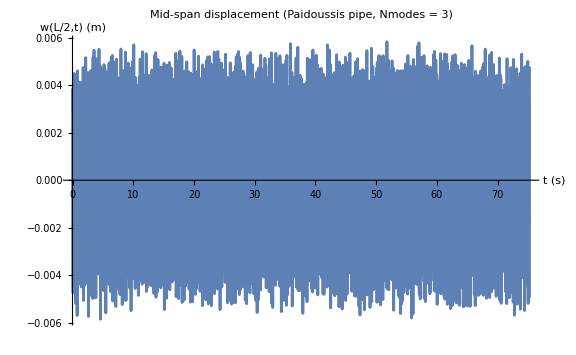

```mathematica
(* =====================================================*)(*Paidoussis simply-supported pipe with*)(*geometric nonlinearity (Galerkin,Nmodes=5)*)(* =====================================================*)
Clear["Global`*"];

(*----------1. Parameters----------*)

L=1.0;      (*pipe length[m]*)
Douter=0.01;     (*outer diameter[m]*)
Dinner=0.009;    (*inner diameter[m]*)

EYoung=2.06*10^11; (*Young's modulus of steel[Pa]*)
rhoS=7850.;      (*density of steel[kg/m^3]*)
rhoF=1000.;      (*density of water[kg/m^3]*)

AreaPipe=Pi/4 (Douter^2-Dinner^2);  (*pipe wall area*)
AreaFluid=Pi/4 Dinner^2;               (*fluid area*)

Isec=Pi/64 (Douter^4-Dinner^4);     (*2nd moment of area*)
mLine=rhoS*AreaPipe+rhoF*AreaFluid;  (*mass per unit length*)

T0=0.0;    (*axial pre-tension (拉力为正)*)

cDamp=0.3;    (*distributed viscous damping c in PDE:c w_t*)

(*flow speed with cosine perturbation:U(t)=U0+dU cos(Omega t)*)
U0=80;
dU=5;
Omega=13.29*2*Pi;   (*you can change this*)

U[t_]:=U0+dU Cos[Omega t];

(*number of modes*)
Nmodes=3;

(*----------2. Mode shapes (simply supported)----------*)

phi[n_,x_]:=Sin[n*Pi*x/L];

(*----------3. Galerkin matrices----------*)

(*Mass matrix:M_ij=∫_0^L mLine*phi_i*phi_j dx*)
Mmat=Table[mLine Integrate[phi[i,x]*phi[j,x],{x,0,L}],{i,1,Nmodes},{j,1,Nmodes}]//Simplify;



(*Bending stiffness:Kb_ij=∫EI*phi_i''*phi_j'' dx*)
Kbend=Table[EYoung*Isec Integrate[D[phi[i,x],{x,2}]*D[phi[j,x],{x,2}],{x,0,L}],{i,1,Nmodes},{j,1,Nmodes}]//Simplify;



(*Axial integral (used for both linear axial stiffness and geometric nonlinearity):KaxInt_ij=∫phi_i'*phi_j' dx*)
KaxInt=Table[Integrate[D[phi[i,x],x]*D[phi[j,x],x],{x,0,L}],{i,1,Nmodes},{j,1,Nmodes}]//Simplify;


(*Gyroscopic/Coriolis matrix:G_ij=∫phi_i*phi_j' dx*)
Gmat=Table[Integrate[phi[i,x]*D[phi[j,x],x],{x,0,L}],{i,1,Nmodes},{j,1,Nmodes}]//Simplify;



(*For geometric nonlinearity:J_ij=∫phi_i*phi_j'' dx*)
Jmat=Table[Integrate[phi[i,x]*D[phi[j,x],{x,2}],{x,0,L}],{i,1,Nmodes},{j,1,Nmodes}]//Simplify;



(*Damping matrix:from c w_t->C_ij=∫c phi_i phi_j dx but M_ij=∫mLine phi_i phi_j dx,so C=(c/mLine) M*)
Cmat=(cDamp/mLine) Mmat;


(*Optional consistency check for simply-supported sin modes:for sin(nπx/L),one should have J≈-KaxInt*)

MatrixForm[Simplify[Jmat+KaxInt]];

(*----------4. Time-dependent linear stiffness (Paidoussis)----------*)

(*PDE linear part:...+[T0-rhoF Af U(t)^2] w_xx+EI w_xxxx...*)

Klin[t_]:=Kbend+(T0-rhoF*AreaFluid*U[t]^2) KaxInt;

(*----------5. Geometric nonlinearity (Paidoussis form)----------*)

(*PDE:-(E A/(2L)) (∫_0^L w_x^2 dx) w_xx After Galerkin:N_i=-(E A/(2L)) (q^T KaxInt q)*Σ_j J_ij q_j*)

(*generalized coordinates vector*)
qvec[t_]:=Array[q[#][t]&,Nmodes];

(*scalar S(t)=∫_0^L w_x^2 dx=q^T KaxInt q*)
Sgeo[t_]:=Sum[q[i][t] q[j][t] KaxInt[[i,j]],{i,1,Nmodes},{j,1,Nmodes}];

(*----------6. Build ODE system:M q''+(...) q'+(...) q+N_geo=0----------*)

eqs=Table[(*inertia:Σ_j M_ij q_j''*)Sum[Mmat[[i,j]] D[q[j][t],{t,2}],{j,1,Nmodes}]+(*damping+Coriolis:Σ_j (C_ij+2ρ_f A_f U(t) G_ij) q_j'*)Sum[(Cmat[[i,j]]+2 rhoF*AreaFluid*U[t]*Gmat[[i,j]])*D[q[j][t],t],{j,1,Nmodes}]+(*linear stiffness:Σ_j Klin(t)_ij q_j*)Sum[Klin[t][[i,j]] q[j][t],{j,1,Nmodes}]+(*geometric nonlinearity:-(E A/(2 L)) S(t) Σ_j J_ij q_j*)(-(EYoung*AreaPipe/(2 L))*Sgeo[t]*Sum[Jmat[[i,j]] q[j][t],{j,1,Nmodes}])==0,{i,1,Nmodes}];

(*----------7. Initial conditions----------*)

(*small initial displacement in the first mode,others zero*)
ics=Join[Table[q[n][0]==If[n==1,0.0029,0],{n,1,Nmodes}],Table[Derivative[1][q[n]][0]==0.0,{n,1,Nmodes}]];

tmax=1000*2*Pi/Omega;  (*simulation time[s]*)

(*For numerical stability,convert matrices to machine numbers*)
Mmat=N[Mmat];
Kbend=N[Kbend];
KaxInt=N[KaxInt];
Gmat=N[Gmat];
Jmat=N[Jmat];
Cmat=N[Cmat];

sol=NDSolve[Join[eqs,ics],Table[q[n],{n,1,Nmodes}],{t,0,tmax}][[1]];

(*----------8. Mid-span displacement response----------*)

wMid[t_]:=Sum[(q[n][t]/. sol)*phi[n,L/2],{n,1,Nmodes}];

midPlot=Plot[wMid[t],{t,0,tmax},AxesLabel->{"t (s)","w(L/2,t) (m)"},PlotLabel->"Mid-span displacement (Paidoussis pipe, Nmodes = "<>ToString[Nmodes]<>")",PlotRange->All,ImageSize->Large];

midPlot
(*(*----------9. 傅里叶变换分析----------*)(*提取时间序列数据*)tSample=Range[0,tmax,tmax/10000]; (*采样点*)
wMidData=wMid/@tSample;

(*去除初始瞬态，只分析稳态响应*)
tStart=tmax/2; (*从一半时间开始分析*)
idxStart=Position[tSample,_?(#>=tStart&),1,1][[1,1]];
tAnalysis=tSample[[idxStart;;-1]];
wAnalysis=wMidData[[idxStart;;-1]];

(*计算采样频率*)
dt=tAnalysis[[2]]-tAnalysis[[1]];
fs=1/dt; (*采样频率*)
n=Length[wAnalysis];

Print["采样频率 fs = ",fs," Hz"];
Print["频率分辨率 Δf = ",fs/n," Hz"];

(*执行傅里叶变换*)
fftResult=Fourier[wAnalysis];
magnitude=Abs[fftResult];

(*频率轴 (只取正频率部分)*)
freqAxis=Table[(i-1)*fs/n,{i,1,Floor[n/2]}];
magnitudePositive=magnitude[[1;;Floor[n/2]]];

(*归一化幅值*)
magnitudeNorm=magnitudePositive/(n/2);

(*找出主要频率峰值*)
peakThreshold=0.01*Max[magnitudeNorm]; (*阈值设为最大值的1%*)
peakPositions=Position[magnitudeNorm,_?(#>peakThreshold&)]//Flatten;
peakFreqs=freqAxis[[peakPositions]];
peakMags=magnitudeNorm[[peakPositions]];

(*按幅值排序，输出前10个主要频率*)
peakData=Transpose[{peakFreqs,peakMags}];
peakDataSorted=Reverse[SortBy[peakData,Last]];
nPeaksToShow=Min[10,Length[peakDataSorted]];

Print["\n========== 主要频率成分 (前",nPeaksToShow,"个) =========="];
Do[Print["频率 ",i,": f = ",NumberForm[peakDataSorted[[i,1]],{8,4}]," Hz,  幅值 = ",NumberForm[peakDataSorted[[i,2]],{8,6}]],{i,1,nPeaksToShow}];

(*打印激励频率作为参考*)
Print["\n参考: 激励频率 Ω/(2π) = ",NumberForm[Omega/(2 Pi),{8,4}]," Hz"];

(*绘制频谱图*)
spectrumPlot=ListLogPlot[Transpose[{freqAxis,magnitudeNorm}],Joined->True,PlotRange->{{0,100},All},(*只显示0-100 Hz*)AxesLabel->{"频率 (Hz)","幅值"},PlotLabel->"中点位移频谱分析",ImageSize->Large,GridLines->Automatic,PlotStyle->{Blue,Thick}];

(*线性尺度的频谱图（更清楚地看低频部分）*)
spectrumPlotLinear=ListPlot[Transpose[{freqAxis,magnitudeNorm}],Joined->True,PlotRange->{{0,100},All},AxesLabel->{"频率 (Hz)","幅值"},PlotLabel->"中点位移频谱分析（线性尺度）",ImageSize->Large,GridLines->Automatic,PlotStyle->{Red,Thick}];

(*显示图形*)
Print["\n对数尺度频谱图:"];
Print[spectrumPlot];
Print["\n线性尺度频谱图:"];
Print[spectrumPlotLinear];

(*组合显示时域和频域*)
combinedPlot=GraphicsGrid[{{midPlot},{spectrumPlotLinear}},ImageSize->Large,Spacings->{0,20}];

Print["\n时域-频域组合图:"];
combinedPlot
*)
```

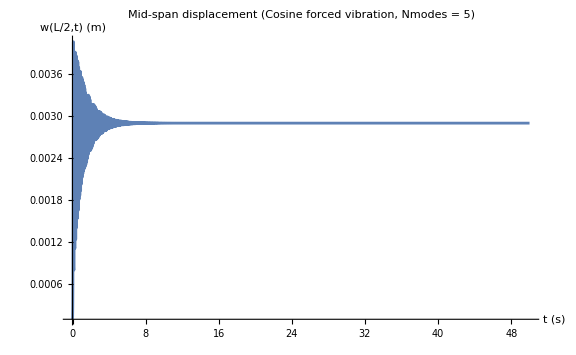

```mathematica
(* =====================================================*)(*Paidoussis simply-supported pipe*)(*Geometric nonlinearity+Forced vibration (cosine)*)(*Galerkin,Nmodes=5*)(* =====================================================*)Clear["Global`*"];

(*----------1. Parameters----------*)

L=1.0;                (*pipe length[m]*)
Douter=0.01;          (*outer diameter[m]*)
Dinner=0.009;         (*inner diameter[m]*)

EYoung=2.06*10^11;    (*Young's modulus[Pa]*)
rhoS=7850.;           (*density of steel[kg/m^3]*)
rhoF=1000.;           (*density of water[kg/m^3]*)

AreaPipe=Pi/4 (Douter^2-Dinner^2);   (*pipe wall area*)
AreaFluid=Pi/4 Dinner^2;               (*fluid area*)

Isec=Pi/64 (Douter^4-Dinner^4);      (*2nd moment of area*)
mLine=rhoS*AreaPipe+rhoF*AreaFluid;  (*mass/length*)

T0=0.0;                                (*axial pre-tension*)
cDamp=0.3;                              (*distributed viscous damping*)

(*Flow speed WITHOUT parametric excitation*)
U0=80;
U[t_]:=U0;      (*constant*)

Nmodes=5;

(*----------2. Mode shapes (simply supported)----------*)

phi[n_,x_]:=Sin[n Pi x/L];

(*----------3. Galerkin matrices----------*)

Mmat=Table[mLine Integrate[phi[i,x]*phi[j,x],{x,0,L}],{i,Nmodes},{j,Nmodes}]//Simplify;

Kbend=Table[EYoung*Isec Integrate[D[phi[i,x],{x,2}]*D[phi[j,x],{x,2}],{x,0,L}],{i,Nmodes},{j,Nmodes}]//Simplify;

KaxInt=Table[Integrate[D[phi[i,x],x]*D[phi[j,x],x],{x,0,L}],{i,Nmodes},{j,Nmodes}]//Simplify;

Gmat=Table[Integrate[phi[i,x]*D[phi[j,x],x],{x,0,L}],{i,Nmodes},{j,Nmodes}]//Simplify;

Jmat=Table[Integrate[phi[i,x]*D[phi[j,x],{x,2}],{x,0,L}],{i,Nmodes},{j,Nmodes}]//Simplify;

Cmat=(cDamp/mLine) Mmat;   (*viscous damping matrix*)

(*----------4. Linear stiffness (constant because U0=const)----------*)

Klin=Kbend+(T0-rhoF*AreaFluid*U0^2) KaxInt;

(*----------5. Geometric nonlinearity----------*)

qvec[t_]:=Array[q[#][t]&,Nmodes];

Sgeo[t_]:=Sum[q[i][t] q[j][t] KaxInt[[i,j]],{i,Nmodes},{j,Nmodes}];

(*----------5'.External forcing (Cosine excitation)----------*)

F0=0.0;           (*forcing amplitude[N]*)
omegaF=4 Pi;            (*forcing frequency[rad/s]*)

Qforc[i_,t_]:=F0*Cos[omegaF t]*phi[i,L/2];

(*----------6. Build ODE system----------*)

eqs=Table[Sum[Mmat[[i,j]] D[q[j][t],{t,2}],{j,Nmodes}]+Sum[(Cmat[[i,j]]+2 rhoF*AreaFluid*U0*Gmat[[i,j]]) D[q[j][t],t],{j,Nmodes}]+Sum[Klin[[i,j]] q[j][t],{j,Nmodes}]+(-(EYoung*AreaPipe/(2 L))*Sgeo[t]*Sum[Jmat[[i,j]] q[j][t],{j,Nmodes}])==Qforc[i,t],{i,Nmodes}];

(*----------7. Initial conditions----------*)

ics=Join[Table[q[n][0]==If[n==1,1.*10^-4,0],{n,Nmodes}],Table[q[n]'[0]==0,{n,Nmodes}]];

tmax=100*2*Pi/omegaF;

(*Convert matrices to machine numbers*)
Mmat=N[Mmat];
Kbend=N[Kbend];
KaxInt=N[KaxInt];
Gmat=N[Gmat];
Jmat=N[Jmat];
Cmat=N[Cmat];
Klin=N[Klin];

sol=NDSolve[Join[eqs,ics],Table[q[n],{n,Nmodes}],{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*----------8. Mid-span displacement----------*)

wMid[t_]:=Sum[(q[n][t]/. sol)*phi[n,L/2],{n,Nmodes}];

midPlot=Plot[wMid[t],{t,0,tmax},AxesLabel->{"t (s)","w(L/2,t) (m)"},PlotLabel->"Mid-span displacement (Cosine forced vibration, Nmodes = "<>ToString[Nmodes]<>")",PlotRange->All,ImageSize->Large];

midPlot
```

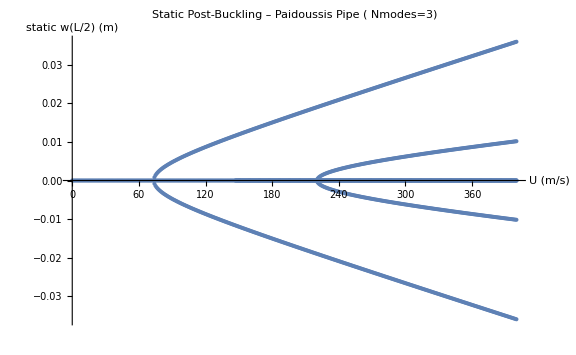

```mathematica
(* =====================================================*)(*Paidoussis pipe:static post-buckling *)(*simply supported,geometric nonlinearity,Galerkin*)(* =====================================================*)Clear["Global`*"];

(*----------1. Parameters----------*)

L=1.0;
Douter=0.01;
Dinner=0.009;

EYoung=2.06*10^11;
rhoS=7850.;
rhoF=1000.;

AreaPipe=Pi/4 (Douter^2-Dinner^2);
AreaFluid=Pi/4 Dinner^2;

Isec=Pi/64 (Douter^4-Dinner^4);
mLine=rhoS*AreaPipe+rhoF*AreaFluid;

T0=0.0;

Nmodes=3;   (*modal truncation for static bifurcation*)

phi[n_,x_]:=Sin[n*Pi*x/L];

(*----------2. Galerkin matrices----------*)

KaxInt=Table[Integrate[D[phi[i,x],x] D[phi[j,x],x],{x,0,L}],{i,1,Nmodes},{j,1,Nmodes}]//N;

Kbend=Table[EYoung*Isec Integrate[D[phi[i,x],{x,2}] D[phi[j,x],{x,2}],{x,0,L}],{i,1,Nmodes},{j,1,Nmodes}]//N;

Jmat=Table[Integrate[phi[i,x] D[phi[j,x],{x,2}],{x,0,L}],{i,1,Nmodes},{j,1,Nmodes}]//N;

(*----------3. Static nonlinear algebraic system----------*)

qVars=Array[q,Nmodes];

(*S(q)=∫w_x^2 dx=q^T KaxInt q*)
Sgeo=qVars.KaxInt.qVars;

(*linear stiffness Klin(U)*)
Klin[U_]:=Kbend+(T0-rhoF*AreaFluid*U^2) KaxInt;

(*static equations:Klin(U) q-(EA/(2L)) S(q) J q=0*)
eqsStatic[U_]:=Module[{K=Klin[U],J=Jmat},Table[Sum[K[[i,j]] qVars[[j]],{j,1,Nmodes}]-(EYoung*AreaPipe/(2 L)) Sgeo*Sum[J[[i,j]] qVars[[j]],{j,1,Nmodes}],{i,1,Nmodes}]];

(*----------4. Solve for equilibrium for U in[0,100]----------*)

uList=Range[0,400,1];
bifData={};

Do[eqsU=eqsStatic[U];
sols=Quiet@NSolve[Thread[eqsU==0],qVars,Reals];
If[sols=!={}&&sols=!={{}},Do[qSol=qVars/. sol;
wMid=Sum[qSol[[n]] phi[n,L/2],{n,1,Nmodes}];
If[NumericQ[wMid]&&Abs[wMid]<0.1,AppendTo[bifData,{U,wMid}]];,{sol,sols}];];,{U,uList}];

(*----------5. Plot bifurcation curve----------*)

ListPlot[bifData,PlotStyle->PointSize[0.005],AxesLabel->{"U (m/s)","static w(L/2) (m)"},PlotLabel->"Static Post-Buckling – Paidoussis Pipe ( Nmodes="<>ToString[Nmodes]<>")",ImageSize->Large]
```

```mathematica
(* ==============================================*)(*Paidoussis 管道（简支）统一前/后屈曲频率计算程序*)(*复制整个块，直接在 Mathematica 里运行即可*)(* ==============================================*)
ClearAll["Global`*"];

(*----------1. 物理参数----------*)
L=1.0;
Douter=0.01;
Dinner=0.009;

EYoung=2.06*10^11;
rhoS=7850.;
rhoF=1000.;

AreaPipe=Pi/4*(Douter^2-Dinner^2);
AreaFluid=Pi/4*Dinner^2;
Isec=Pi/64*(Douter^4-Dinner^4);
mLine=rhoS*AreaPipe+rhoF*AreaFluid;

T0=0.0;
Nmodes=3;   (*Galerkin 模态数*)

(*简支正弦模态*)
phi[n_,x_]:=Sin[n Pi x/L];

(*----------2. Galerkin 矩阵----------*)

(*质量矩阵 Mij=∫mLine phi_i phi_j dx*)
Mmat=Table[mLine Integrate[phi[i,x] phi[j,x],{x,0,L}],{i,1,Nmodes},{j,1,Nmodes}]//N;

(*弯曲刚度 Kbend_ij=∫EI phi_i'' phi_j'' dx*)
Kbend=Table[EYoung*Isec Integrate[D[phi[i,x],{x,2}] D[phi[j,x],{x,2}],{x,0,L}],{i,1,Nmodes},{j,1,Nmodes}]//N;

(*轴向积分 KaxInt_ij=∫phi_i' phi_j' dx*)
KaxInt=Table[Integrate[D[phi[i,x],x] D[phi[j,x],x],{x,0,L}],{i,1,Nmodes},{j,1,Nmodes}]//N;

(*J_ij=∫phi_i phi_j'' dx*)
Jmat=Table[Integrate[phi[i,x] D[phi[j,x],{x,2}],{x,0,L}],{i,1,Nmodes},{j,1,Nmodes}]//N;

qVars=Array[q,Nmodes];

(*----------3. 静态方程& 切线刚度----------*)

(*S(q)=q^T KaxInt q*)
SgeoStatic[q_?VectorQ]:=q.KaxInt.q;

(*线性刚度（给定流速 U）*)
KlinStatic[U_?NumericQ]:=Kbend+(T0-rhoF*AreaFluid*U^2) KaxInt;

(*静态后屈曲方程：Klin(U) q-(EA/(2L)) S(q) J q=0*)
eqsStatic[U_?NumericQ]:=Module[{K},K=KlinStatic[U];
Table[Sum[K[[i,j]] qVars[[j]],{j,1,Nmodes}]-(EYoung*AreaPipe/(2 L)) SgeoStatic[qVars]*Sum[Jmat[[i,j]] qVars[[j]],{j,1,Nmodes}]==0,{i,1,Nmodes}]];

(*几何刚度 Kgeo(q)=-(EA/(2L))[2 (J q)(KaxInt q)^T+S(q) J]*)
Kgeo[q_?VectorQ]:=Module[{S,vJ,vK,mat},S=q.KaxInt.q;(*标量 S(q)*)vJ=Jmat.q;(*向量 J q*)vK=KaxInt.q;(*向量 KaxInt q*)mat=2 Outer[Times,vJ,vK]+S Jmat;
-(EYoung*AreaPipe/(2 L)) mat];

(*----------4. 统一平衡+频率函数----------*)

ClearAll[pipeEquilibriumAndFreq];

(*选平衡构型时的阈值：TolMin：判定“非零后屈曲解”的最小范数 TolMax：排除挠度过大的解（数值发散用）*)
Options[pipeEquilibriumAndFreq]={"TolMin"->10^-6,"TolMax"->0.1};

pipeEquilibriumAndFreq[U_?NumericQ,opts:OptionsPattern[]]:=Module[{tolMin=OptionValue["TolMin"],tolMax=OptionValue["TolMax"],sols,qCandidates,qList,postCandidates,qEq,wMidEq,KlinEq,KgeoEq,Ktan,eigResult,evals,evalsReal,evalsPos,omegas,freqs},Print["\n================ U = ",U," ================="];
(*----4.1 静态平衡求解----*)sols=Quiet@NSolve[eqsStatic[U],qVars,Reals];
qCandidates=(qVars/. sols)//N;
(*只保留“真正的数值向量”的解*)qList=Select[qCandidates,VectorQ[#,NumericQ]&];
If[qList==={},Print["❌ U = ",U," 未找到任何静态平衡解。"];
Return[$Failed];];
(*优先选择“非零后屈曲解”：Norm 在 (tolMin,tolMax) 之间*)postCandidates=Select[qList,tolMin<Norm[#]<tolMax&];
qEq=If[postCandidates=!={},(*存在后屈曲解：选范数最小的那支*)First@SortBy[postCandidates,Norm],(*没有后屈曲解：退回到范数最小的平衡解（通常是 q=0）*)First@SortBy[qList,Norm]];
wMidEq=Sum[qEq[[n]] phi[n,L/2],{n,1,Nmodes}];
Print["静态平衡 q_eq = ",qEq];
Print["中点挠度 w(L/2) = ",wMidEq," m"];
(*----4.2 切线刚度矩阵----*)KlinEq=KlinStatic[U];
KgeoEq=Kgeo[qEq];
Ktan=N[KlinEq+KgeoEq];
Ktan=Chop[Ktan,10^-12];
Print["\n切线刚度矩阵 K_tan:"];
Print[MatrixForm[Ktan]];
(*----4.3 特征值问题：统一前/后屈曲频率----*)eigResult=Eigensystem[{Ktan,Mmat}];
evals=eigResult[[1]]//N;
evalsReal=Chop[evals,10^-10];
(*只保留正的特征值*)evalsPos=Sort@Select[evalsReal,#>0&];
If[evalsPos==={},Print["\n⚠ 没有正的特征值：当前构型可能失稳或数值有问题。"];
omegas={};freqs={};,omegas=Sqrt[evalsPos];
freqs=omegas/(2 Pi);];
Print["\n---- 小振动固有频率 (U = ",U,") ----"];
If[omegas==={},Print["(无正实频率输出)"],Do[Print["Mode ",i,":  ω = ",NumberForm[omegas[[i]],{8,4}]," rad/s   f = ",NumberForm[freqs[[i]],{8,4}]," Hz"],{i,Length[omegas]}];];
Print["==================================="];
<|"U"->U,"qEq"->qEq,"wMid"->wMidEq,"Ktan"->Ktan,"omegas"->omegas,"freqs"->freqs|>];

(*----------5. 示例调用----------*)


res=pipeEquilibriumAndFreq[72];

(*结果结构：res["U"]——当前流速 res["qEq"]——选中的平衡构型系数 q_eq res["wMid"]——中点挠度 w(L/2) res["Ktan"]——切线刚度矩阵 res["freqs"]——正的固有频率列表 (Hz)*)


13.2984/4.3091
184.8717/13.2984
```

================ U = 72 =================

静态平衡 q_eq = {0.,0.,0.}

中点挠度 w(L/2) = 0. m

切线刚度矩阵 K_tan:

(66.2515 | 0 | 0
0 | 20589.5 | 0
0 | 0 | 122543.)

---- 小振动固有频率 (U = 72) ----

Mode 1:  ω = 27.0746 rad/s   f = 4.3091 Hz

Mode 2:  ω = 477.2958 rad/s   f = 75.9640 Hz

Mode 3:  ω = 1164.4192 rad/s   f = 185.3231 Hz

===================================

3.08612

13.9018

```mathematica
(* =====================================================*)(*Paidoussis 输流管数据集生成-广义坐标版本*)
SetDirectory@NotebookDirectory[];
ClearAll["Global`*"];

(* =====================================================*)
(*0. 工具函数：连续零平台判定*)
(* =====================================================*)

isZeroState[q_,qdot_,qddot_,tol_]:=Norm[q]<tol&&Norm[qdot]<tol&&Norm[qddot]<tol;

findZeroPlateauStart[qVals_,qdotVals_,qddotVals_,tol_,Nzero_]:=Module[{flags},flags=MapThread[isZeroState[#1,#2,#3,tol]&,{qVals,qdotVals,qddotVals}];
FirstCase[Partition[flags,Nzero,1],{True..}:>First@FirstPosition[flags,True],Missing["NotFound"]]];

(* =====================================================*)
(*1. 物理参数*)
(* =====================================================*)

L=1.0;
Douter=0.01;
Dinner=0.009;

EYoung=2.06*10^11;
rhoS=7850.;
rhoF=1000.;

qInitSmallAmp=0.001;
qInitTol=10^-8;

AreaPipe=Pi/4 (Douter^2-Dinner^2);
AreaFluid=Pi/4 Dinner^2;
Isec=Pi/64 (Douter^4-Dinner^4);

mLine=rhoS*AreaPipe+rhoF*AreaFluid;

T0=0.0;
cDamp=0.3;

Nmodes=3;
NmodesStatic=3;

Ucr=73.5;

(* =====================================================*)
(*2. 模态函数（简支）*)
(* =====================================================*)

phi[n_,x_]:=Sin[n*Pi*x/L];

(* =====================================================*)
(*3. Galerkin 矩阵（动力学）*)
(* =====================================================*)

Mmat=Table[mLine Integrate[phi[i,x]*phi[j,x],{x,0,L}],{i,1,Nmodes},{j,1,Nmodes}]//N;

Kbend=Table[EYoung*Isec Integrate[D[phi[i,x],{x,2}] D[phi[j,x],{x,2}],{x,0,L}],{i,1,Nmodes},{j,1,Nmodes}]//N;

KaxInt=Table[Integrate[D[phi[i,x],x] D[phi[j,x],x],{x,0,L}],{i,1,Nmodes},{j,1,Nmodes}]//N;

Gmat=Table[Integrate[phi[i,x] D[phi[j,x],x],{x,0,L}],{i,1,Nmodes},{j,1,Nmodes}]//N;

Jmat=Table[Integrate[phi[i,x] D[phi[j,x],{x,2}],{x,0,L}],{i,1,Nmodes},{j,1,Nmodes}]//N;

Cmat=(cDamp/mLine) Mmat;

(* =====================================================*)
(*3.1 几何刚度*)
(* =====================================================*)

Kgeo[q_?VectorQ]:=Module[{S,vJ,vK},S=q.KaxInt.q;
vJ=Jmat.q;
vK=KaxInt.q;
-(EYoung*AreaPipe/(2 L)) (2 Outer[Times,vJ,vK]+S Jmat)];

(* =====================================================*)
(*4. 静态后屈曲（用于初值）*)
(* =====================================================*)

KaxIntStatic=KaxInt[[;;NmodesStatic, ;;NmodesStatic]];
KbendStatic=Kbend[[;;NmodesStatic, ;;NmodesStatic]];
JmatStatic=Jmat[[;;NmodesStatic, ;;NmodesStatic]];

qVarsStatic=Array[qs,NmodesStatic];
SgeoStatic=qVarsStatic.KaxIntStatic.qVarsStatic;

KlinStatic[U_]:=KbendStatic+(T0-rhoF*AreaFluid*U^2) KaxIntStatic;

eqsStatic[U_]:=Table[Sum[KlinStatic[U][[i,j]] qVarsStatic[[j]],{j,NmodesStatic}]-(EYoung*AreaPipe/(2 L)) SgeoStatic Sum[JmatStatic[[i,j]] qVarsStatic[[j]],{j,NmodesStatic}],{i,NmodesStatic}];

ComputeStaticEquilibrium[U_]:=Module[{sols,valid={},qSol,wMid},sols=Quiet@NSolve[eqsStatic[U]==0,qVarsStatic,Reals];
Do[qSol=qVarsStatic/. sol;
wMid=Sum[qSol[[n]] phi[n,L/2],{n,NmodesStatic}];
If[NumericQ[wMid]&&Abs[wMid]<0.05,AppendTo[valid,qSol]],{sol,sols}];
If[valid==={},{Table[0.,NmodesStatic]},valid]];

ExtendToFullModes[qStatic_]:=PadRight[qStatic,Nmodes,0.];

(* =====================================================*)
(*4.1 一阶固有频率*)
(* =====================================================*)

FirstNaturalFrequency[U_]:=Module[{qEq,Ktan,evals},qEq=ExtendToFullModes[First@ComputeStaticEquilibrium[U]];
Ktan=Kbend+(T0-rhoF*AreaFluid*U^2) KaxInt+Kgeo[qEq];
evals=Eigenvalues[{Ktan,Mmat}];
First@Sqrt@Sort@Select[Re[evals],#>0&]];

(* =====================================================*)
(*5. 数据生成（含零平台截断）*)
(* =====================================================*)

GenerateDataFromParams[U0_,dU_,Omega_]:=Module[{U,Udot,Klin,qvec,Sgeo,eqs,ics,tmax,h,sol,tgrid,qSol,qdotSol,qddotSol,qVals,qdotVals,qddotVals,tgridUsed,zeroStartIdx,Nzero=20,data,list,allResults={},staticSols,initConfigList},staticSols=ComputeStaticEquilibrium[U0];
Do[initConfigList=If[Norm[ExtendToFullModes[staticSol]]<qInitTol,{Join[{+qInitSmallAmp},ConstantArray[0.,Nmodes-1]],Join[{-qInitSmallAmp},ConstantArray[0.,Nmodes-1]]},{ExtendToFullModes[staticSol]}];
Do[U[t_]:=U0+dU Cos[Omega t];
Udot[t_]:=-dU Omega Sin[Omega t];
Klin[t_]:=Kbend+(T0-rhoF*AreaFluid*U[t]^2) KaxInt;
qvec[t_]:=Array[q[#][t]&,Nmodes];
Sgeo[t_]:=Sum[q[i][t] q[j][t] KaxInt[[i,j]],{i,Nmodes},{j,Nmodes}];
eqs=Table[Sum[Mmat[[i,j]] q[j]''[t],{j,Nmodes}]+Sum[rhoF*AreaFluid*Udot[t] Gmat[[i,j]] q[j][t],{j,Nmodes}]+Sum[(Cmat[[i,j]]+2 rhoF*AreaFluid*U[t] Gmat[[i,j]]) q[j]'[t],{j,Nmodes}]+Sum[Klin[t][[i,j]] q[j][t],{j,Nmodes}]-(EYoung*AreaPipe/(2 L)) Sgeo[t] Sum[Jmat[[i,j]] q[j][t],{j,Nmodes}]==0,{i,Nmodes}];
ics=Join[Table[q[n][0]==initCfg[[n]],{n,Nmodes}],Table[q[n]'[0]==0.2,{n,Nmodes}]];
tmax=50*2*Pi/Omega;
h=2*Pi/Omega/200;
tgrid=Range[0,tmax,h];
sol=Quiet@NDSolve[Join[eqs,ics],Join[Table[q[n],{n,Nmodes}],Table[q[n]',{n,Nmodes}],Table[q[n]'',{n,Nmodes}]],{t,0,tmax},MaxStepSize->h/2,Method->{"StiffnessSwitching"}][[1]];
qSol=Table[q[n]/. sol,{n,Nmodes}];
qdotSol=Table[q[n]'/. sol,{n,Nmodes}];
qddotSol=Table[q[n]''/. sol,{n,Nmodes}];
qVals=Table[Table[qSol[[n]][tt],{n,1,Nmodes}],{tt,tgrid}];

qdotVals=Table[Table[qdotSol[[n]][tt],{n,1,Nmodes}],{tt,tgrid}];

qddotVals=Table[Table[qddotSol[[n]][tt],{n,1,Nmodes}],{tt,tgrid}];

zeroStartIdx=findZeroPlateauStart[qVals,qdotVals,qddotVals,qInitTol,Nzero];
tgridUsed=If[zeroStartIdx===Missing["NotFound"],tgrid,tgrid[[;;zeroStartIdx+Nzero-1]]];
qVals=qVals[[;;Length[tgridUsed]]];
qdotVals=qdotVals[[;;Length[tgridUsed]]];
qddotVals=qddotVals[[;;Length[tgridUsed]]];
data=Table[Join[{U0,dU Cos[Omega tgridUsed[[i]]]},qVals[[i]],qdotVals[[i]],qddotVals[[i]]],{i,Length[tgridUsed]}];
list=Table[data[[i,1;;2+2 Nmodes]]->data[[i,2+2 Nmodes+1;;-1]],{i,Length[data]}];
allResults=Join[allResults,list];,{initCfg,initConfigList}],{staticSol,staticSols}];
If[allResults==={},$Failed,allResults]];

(*====================6. 工况网格：全局+局部加密====================*)(*----------全局网格（你原来的设置）----------*)
(* =====================================================*)(*6. 工况网格：全局+局部补丁（joint1 形式）*)(* =====================================================*)(*----------6.1 全局工况列表（你原来的）----------*)
U0ListGlobal=Join[Range[70,72,1],Range[73,74,0.25],Range[75,81,1]];
dUListGlobal=Range[0,1.1,0.1];
facListGlobal=Range[0.9,1.1,0.1];

(*----------6.2 局部补丁列表：不扫U0，只在指定U0点补丁扫 dU+fac----------*)
useLocalPatch=True;

U0ListLocal={80.0};                 (*只在这些U0点补丁；多个点如 {73.5,74.0,74.5}*)
dUListLocal=Join[Range[0,1.1,0.1],Range[1.12,1.4,0.001]];   (*你自己调*)
facListLocal=Join[Range[0.9,1.1,0.1](*,Range[0.9*5.675,5.675*1.1,0.1*5.675],Range[0.9*13.9,1.1*13.9,13.9*0.1]*)]; 

(*----------6.3 生成 joint1：{U0,dU,fac}----------*)
joint1Global=Flatten[Table[{U0,dU,fac},{U0,U0ListGlobal},{dU,dUListGlobal},{fac,facListGlobal}],2];

joint1Local=If[useLocalPatch,Flatten[Table[{U0,dU,fac},{U0,U0ListLocal},{dU,dUListLocal},{fac,facListLocal}],2],{}];

(*----------6.4 合并+去重（建议在 joint1 层去重，避免 omega1 数值抖动导致“看似重复却删不掉”）----------*)
tolU0=10^-6;
toldU=10^-6;
tolfac=10^-6;

keyJoint1[{U0_,dU_,fac_}]:={Round[N@U0,tolU0],Round[N@dU,toldU],Round[N@fac,tolfac]};

joint1All=DeleteDuplicatesBy[Join[joint1Global,joint1Local],keyJoint1];

(*----------6.5 把 joint1 映射成你原来的 {"Omega",{U0,dU,Omega}} 工况----------*)
ClearAll[omega1Cached];
omega1Cached[U_?NumericQ]:=omega1Cached[U]=FirstNaturalFrequency[U];

gridCases=Map[Function[{j},Module[{U0=j[[1]],dU=j[[2]],fac=j[[3]],w1,Om},w1=omega1Cached[U0];
If[Not[NumericQ[w1]]||w1<=0,Nothing,Om=fac*w1;
{"Omega",{U0,dU,Om}}]]],joint1All];

(*你后续如果用 allCases/totalCombinations 就保持接口一致*)
allCases=gridCases;
totalCombinations=Length[allCases];

Print["==================数据生成配置(第6节)=================="];
Print["全局 joint1 数: ",Length[joint1Global]];
Print["局部补丁 joint1 数: ",Length[joint1Local]];
Print["合并去重后 joint1 数: ",Length[joint1All]];
Print["最终 allCases 数: ",totalCombinations];


(*----------7. 并行生成数据：逐工况保存----------*)LaunchKernels[];
Print["并行内核数: ",$KernelCount];

DistributeDefinitions[isZeroState,findZeroPlateauStart,phi,Mmat,Kbend,KaxInt,Gmat,Jmat,Cmat,Kgeo,ComputeStaticEquilibrium,ExtendToFullModes,FirstNaturalFrequency,GenerateDataFromParams,L,Douter,Dinner,EYoung,rhoS,rhoF,qInitSmallAmp,qInitTol,AreaPipe,AreaFluid,Isec,mLine,T0,cDamp,Nmodes,NmodesStatic,Ucr,U0List,dUList,OmegaFactors,gridCases,allCases,totalCombinations];

SeedRandom[Automatic];
ParallelEvaluate[SeedRandom[Automatic]];

outDir=FileNameJoin[{Directory[],"pipe_flow_cases_parallel"}];
If[!DirectoryQ[outDir],CreateDirectory[outDir]];

SetSharedVariable[currentCombination,successCount,failedCount];
currentCombination=0;successCount=0;failedCount=0;
counterLock=Unique["counterLock$"];

Print["\n==================开始生成数据（并行，逐工况保存）=================="];
Print["总工况数: ",totalCombinations];
Print["输出目录: ",outDir];

solveOneCaseParallel[case_]:=Module[{U0,dU,Omega,samples,shuffled,splitIdx1,splitIdx2,base,fTrain,fVal,fTest},{U0,dU,Omega}=case[[2]];
SeedRandom[Mod[Hash[{U0,dU,Omega}],2^31-1]];
samples=GenerateDataFromParams[U0,dU,Omega];
If[samples===$Failed||samples==={},CriticalSection[counterLock,failedCount++;currentCombination++;
If[Mod[currentCombination,10]==0||currentCombination==totalCombinations,Print["进度: ",currentCombination,"/",totalCombinations," (",NumberForm[100. currentCombination/Max[1,totalCombinations],{4,1}],"%)","  成功: ",successCount,"  失败: ",failedCount];];];
Return[<|"ok"->False,"case"->case|>];];
shuffled=RandomSample[samples];
splitIdx1=Round[0.7 Length[shuffled]];
splitIdx2=Round[0.85 Length[shuffled]];
base=StringReplace[ToString@Row[{"U0_",NumberForm[U0,{Infinity,4}],"_dU_",NumberForm[dU,{Infinity,6}],"_Om_",NumberForm[Omega,{Infinity,6}]}],{" "->"","."->"p","-"->"m"}];
fTrain=FileNameJoin[{outDir,base<>"_train.mx"}];
fVal=FileNameJoin[{outDir,base<>"_val.mx"}];
fTest=FileNameJoin[{outDir,base<>"_test.mx"}];
Export[fTrain,shuffled[[1;;splitIdx1]],"MX"];
Export[fVal,shuffled[[splitIdx1+1;;splitIdx2]],"MX"];
Export[fTest,shuffled[[splitIdx2+1;;-1]],"MX"];
Clear[samples,shuffled];
CriticalSection[counterLock,successCount++;currentCombination++;
If[Mod[currentCombination,10]==0||currentCombination==totalCombinations,Print["进度: ",currentCombination,"/",totalCombinations," (",NumberForm[100. currentCombination/Max[1,totalCombinations],{4,1}],"%)","  成功: ",successCount,"  失败: ",failedCount];];];
<|"ok"->True,"case"->case,"files"->{fTrain,fVal,fTest}|>];

results=ParallelMap[solveOneCaseParallel,allCases,Method->"FinestGrained"];

Print["\n成功: ",successCount,"/",totalCombinations," (",NumberForm[100. successCount/Max[1,totalCombinations],{4,1}],"%)"];
Print["失败: ",failedCount];
Print["\n✅ 已逐工况保存到: ",outDir];


(*----------8并行读回+按工况固定数量抽样（无 cap）----------*)
Print["\n==================并行读回 + 按工况固定抽样=================="];

(*★ 每个工况抽多少：只需要改这三个*)
kTrainPerCase=2000;
kValPerCase=0.1*kTrainPerCase;
kTestPerCase=0.1*kTrainPerCase;

trainFiles=FileNames["*_train.mx",outDir];
valFiles=FileNames["*_val.mx",outDir];
testFiles=FileNames["*_test.mx",outDir];

Print["发现文件数: train=",Length[trainFiles],"  val=",Length[valFiles],"  test=",Length[testFiles]];

If[trainFiles==={}||valFiles==={}||testFiles==={},Print["❌ outDir 下未找到 train/val/test 文件：",outDir];
Abort[];];

(*打乱文件顺序，避免顺序偏置*)
trainFiles=RandomSample[trainFiles];
valFiles=RandomSample[valFiles];
testFiles=RandomSample[testFiles];

inputDim=2+2*Nmodes;
outputDim=Nmodes;

(*----------Welford 在线统计（主核）----------*)
welfordInit[dim_]:=<|"n"->0,"mean"->ConstantArray[0.,dim],"M2"->ConstantArray[0.,dim]|>;
welfordUpdate[st_,x_?VectorQ]:=Module[{n1,d,mean1,d2,M21},n1=st["n"]+1;
d=x-st["mean"];
mean1=st["mean"]+d/n1;
d2=x-mean1;
M21=st["M2"]+d*d2;
<|"n"->n1,"mean"->mean1,"M2"->M21|>];
welfordFinalize[st_]:=Module[{n=st["n"],var},var=If[n>=2,st["M2"]/(n-1),ConstantArray[0.,Length[st["mean"]]]];
<|"n"->n,"mean"->st["mean"],"std"->(Sqrt[var]/. 0.->1.)|>];

(*----------并行：单文件->抽 k 个->返回----------*)
sampleOneFile[file_,k_]:=Module[{data,len},data=Quiet@Check[Import[file,"MX"],$Failed];
If[data===$Failed,Return[{}]];
len=Length[data];
If[len==0,Return[{}]];
SeedRandom[Mod[Hash[file],2^31-1]];
RandomSample[data,Min[k,len]]];

(*----------train：并行读取----------*)
trainChunks=ParallelMap[sampleOneFile[#,kTrainPerCase]&,trainFiles,Method->"FinestGrained"];
trainData=Flatten[trainChunks,1];
Clear[trainChunks];

(*在线统计（只在主核做，安全）*)
stIn=welfordInit[inputDim];
stOut=welfordInit[outputDim];
Do[stIn=welfordUpdate[stIn,trainData[[i,1]]];
stOut=welfordUpdate[stOut,trainData[[i,2]]];,{i,Length[trainData]}];

(*----------val----------*)
valChunks=ParallelMap[sampleOneFile[#,kValPerCase]&,valFiles,Method->"FinestGrained"];
valData=Flatten[valChunks,1];
Clear[valChunks];

(*----------test----------*)
testChunks=ParallelMap[sampleOneFile[#,kTestPerCase]&,testFiles,Method->"FinestGrained"];
testData=Flatten[testChunks,1];
Clear[testChunks];

If[trainData==={}||valData==={}||testData==={},Print["❌ 抽样后存在空集：请检查 k*PerCase 或文件内容"];
Abort[];];

finIn=welfordFinalize[stIn];
finOut=welfordFinalize[stOut];
inputMean=finIn["mean"];inputStd=finIn["std"];
targetMean=finOut["mean"];targetStd=finOut["std"];

Print["\n最终规模（并行，每工况固定抽样）:"];
Print["训练集: ",Length[trainData],"  ≈ ",Length[trainFiles]," × ",kTrainPerCase];
Print["验证集: ",Length[valData],"  ≈ ",Length[valFiles]," × ",kValPerCase];
Print["测试集: ",Length[testData],"  ≈ ",Length[testFiles]," × ",kTestPerCase];

Print["\n在线统计（基于 trainData）:"];
Print["输入均值(前6): ",NumberForm[inputMean[[;;Min[6,Length[inputMean]]]],{6,4}]];
Print["输入标准差(前6): ",NumberForm[inputStd[[;;Min[6,Length[inputStd]]]],{6,4}]];
Print["输出均值: ",NumberForm[targetMean,{8,4}]];
Print["输出标准差: ",NumberForm[targetStd,{8,4}]];

Export[FileNameJoin[{Directory[],"trainData_pipe_flow_generalized_cos.mx"}],trainData,"MX"];
Export[FileNameJoin[{Directory[],"valData_pipe_flow_generalized_cos.mx"}],valData,"MX"];
Export[FileNameJoin[{Directory[],"testData_pipe_flow_generalized_cos.mx"}],testData,"MX"];

normParams=<|"inputMean"->inputMean,"inputStd"->inputStd,"targetMean"->targetMean,"targetStd"->targetStd,"U0List"->U0List,"dUList"->dUList,"OmegaFactors"->OmegaFactors,"Ucr"->Ucr,"L"->L,"Douter"->Douter,"Dinner"->Dinner,"cDamp"->cDamp,"Nmodes"->Nmodes,"NmodesStatic"->NmodesStatic,"successCount"->successCount,"failedCount"->failedCount,"inputDim"->inputDim,"outputDim"->outputDim,"kTrainPerCase"->kTrainPerCase,"kValPerCase"->kValPerCase,"kTestPerCase"->kTestPerCase|>;
Export[FileNameJoin[{Directory[],"normParams_pipe_flow_generalized_cos.mx"}],normParams,"MX"];

Print["\n✅ 完成：并行逐工况读取 → 固定抽样 → 合并 → 在线统计 → 保存"];
```

==================数据生成配置(第6节)==================

全局 joint1 数: 540

局部补丁 joint1 数: 879

合并去重后 joint1 数: 1383

最终 allCases 数: 1383

并行内核数: 24

==================开始生成数据（并行，逐工况保存）==================

总工况数: 1383

输出目录: C:\Users\Lpp\Desktop\data-drivenpipe\code_pipe\pipe_flow_cases_parallel

进度: 10/1383 (0.7%)  成功: 10  失败: 0

进度: 20/1383 (1.4%)  成功: 20  失败: 0

进度: 30/1383 (2.2%)  成功: 30  失败: 0

进度: 40/1383 (2.9%)  成功: 40  失败: 0

进度: 50/1383 (3.6%)  成功: 50  失败: 0

进度: 60/1383 (4.3%)  成功: 60  失败: 0

进度: 70/1383 (5.1%)  成功: 70  失败: 0

进度: 80/1383 (5.8%)  成功: 80  失败: 0

进度: 90/1383 (6.5%)  成功: 90  失败: 0

进度: 100/1383 (7.2%)  成功: 100  失败: 0

进度: 110/1383 (8.0%)  成功: 110  失败: 0

进度: 120/1383 (8.7%)  成功: 120  失败: 0

进度: 130/1383 (9.4%)  成功: 130  失败: 0

进度: 140/1383 (10.1%)  成功: 140  失败: 0

进度: 150/1383 (10.8%)  成功: 150  失败: 0

进度: 160/1383 (11.6%)  成功: 160  失败: 0

进度: 170/1383 (12.3%)  成功: 170  失败: 0

进度: 180/1383 (13.0%)  成功: 180  失败: 0

进度: 190/1383 (13.7%)  成功: 190  失败: 0

进度: 200/1383 (14.5%)  成功: 200  失败: 0

进度: 210/1383 (15.2%)  成功: 210  失败: 0

进度: 220/1383 (15.9%)  成功: 220  失败: 0

进度: 230/1383 (16.6%)  成功: 230  失败: 0

进度: 240/1383 (17.4%)  成功: 240  失败: 0

进度: 250/1383 (18.1%)  成功: 250  失败: 0

进度: 260/1383 (18.8%)  成功: 260  失败: 0

进度: 270/1383 (19.5%)  成功: 270  失败: 0

进度: 280/1383 (20.2%)  成功: 280  失败: 0

进度: 290/1383 (21.0%)  成功: 290  失败: 0

进度: 300/1383 (21.7%)  成功: 300  失败: 0

进度: 310/1383 (22.4%)  成功: 310  失败: 0

进度: 320/1383 (23.1%)  成功: 320  失败: 0

进度: 330/1383 (23.9%)  成功: 330  失败: 0

进度: 340/1383 (24.6%)  成功: 340  失败: 0

进度: 350/1383 (25.3%)  成功: 350  失败: 0

进度: 360/1383 (26.0%)  成功: 360  失败: 0

进度: 370/1383 (26.8%)  成功: 370  失败: 0

进度: 380/1383 (27.5%)  成功: 380  失败: 0

进度: 390/1383 (28.2%)  成功: 390  失败: 0

进度: 400/1383 (28.9%)  成功: 400  失败: 0

进度: 410/1383 (29.6%)  成功: 410  失败: 0

进度: 420/1383 (30.4%)  成功: 420  失败: 0

进度: 430/1383 (31.1%)  成功: 430  失败: 0

进度: 440/1383 (31.8%)  成功: 440  失败: 0

进度: 450/1383 (32.5%)  成功: 450  失败: 0

进度: 460/1383 (33.3%)  成功: 460  失败: 0

进度: 470/1383 (34.0%)  成功: 470  失败: 0

进度: 480/1383 (34.7%)  成功: 480  失败: 0

进度: 490/1383 (35.4%)  成功: 490  失败: 0

进度: 500/1383 (36.2%)  成功: 500  失败: 0

进度: 510/1383 (36.9%)  成功: 510  失败: 0

进度: 520/1383 (37.6%)  成功: 520  失败: 0

进度: 530/1383 (38.3%)  成功: 530  失败: 0

进度: 540/1383 (39.0%)  成功: 540  失败: 0

进度: 550/1383 (39.8%)  成功: 550  失败: 0

进度: 560/1383 (40.5%)  成功: 560  失败: 0

进度: 570/1383 (41.2%)  成功: 570  失败: 0

进度: 580/1383 (41.9%)  成功: 580  失败: 0

进度: 590/1383 (42.7%)  成功: 590  失败: 0

进度: 600/1383 (43.4%)  成功: 600  失败: 0

进度: 610/1383 (44.1%)  成功: 610  失败: 0

进度: 620/1383 (44.8%)  成功: 620  失败: 0

进度: 630/1383 (45.6%)  成功: 630  失败: 0

进度: 640/1383 (46.3%)  成功: 640  失败: 0

进度: 650/1383 (47.0%)  成功: 650  失败: 0

进度: 660/1383 (47.7%)  成功: 660  失败: 0

进度: 670/1383 (48.4%)  成功: 670  失败: 0

进度: 680/1383 (49.2%)  成功: 680  失败: 0

进度: 690/1383 (49.9%)  成功: 690  失败: 0

进度: 700/1383 (50.6%)  成功: 700  失败: 0

进度: 710/1383 (51.3%)  成功: 710  失败: 0

进度: 720/1383 (52.1%)  成功: 720  失败: 0

进度: 730/1383 (52.8%)  成功: 730  失败: 0

进度: 740/1383 (53.5%)  成功: 740  失败: 0

进度: 750/1383 (54.2%)  成功: 750  失败: 0

进度: 760/1383 (55.0%)  成功: 760  失败: 0

进度: 770/1383 (55.7%)  成功: 770  失败: 0

进度: 780/1383 (56.4%)  成功: 780  失败: 0

进度: 790/1383 (57.1%)  成功: 790  失败: 0

进度: 800/1383 (57.8%)  成功: 800  失败: 0

进度: 810/1383 (58.6%)  成功: 810  失败: 0

进度: 820/1383 (59.3%)  成功: 820  失败: 0

进度: 830/1383 (60.0%)  成功: 830  失败: 0

进度: 840/1383 (60.7%)  成功: 840  失败: 0

进度: 850/1383 (61.5%)  成功: 850  失败: 0

进度: 860/1383 (62.2%)  成功: 860  失败: 0

进度: 870/1383 (62.9%)  成功: 870  失败: 0

进度: 880/1383 (63.6%)  成功: 880  失败: 0

进度: 890/1383 (64.4%)  成功: 890  失败: 0

进度: 900/1383 (65.1%)  成功: 900  失败: 0

进度: 910/1383 (65.8%)  成功: 910  失败: 0

进度: 920/1383 (66.5%)  成功: 920  失败: 0

进度: 930/1383 (67.2%)  成功: 930  失败: 0

进度: 940/1383 (68.0%)  成功: 940  失败: 0

进度: 950/1383 (68.7%)  成功: 950  失败: 0

进度: 960/1383 (69.4%)  成功: 960  失败: 0

进度: 970/1383 (70.1%)  成功: 970  失败: 0

进度: 980/1383 (70.9%)  成功: 980  失败: 0

进度: 990/1383 (71.6%)  成功: 990  失败: 0

进度: 1000/1383 (72.3%)  成功: 1000  失败: 0

进度: 1010/1383 (73.0%)  成功: 1010  失败: 0

进度: 1020/1383 (73.8%)  成功: 1020  失败: 0

进度: 1030/1383 (74.5%)  成功: 1030  失败: 0

进度: 1040/1383 (75.2%)  成功: 1040  失败: 0

进度: 1050/1383 (75.9%)  成功: 1050  失败: 0

进度: 1060/1383 (76.6%)  成功: 1060  失败: 0

进度: 1070/1383 (77.4%)  成功: 1070  失败: 0

进度: 1080/1383 (78.1%)  成功: 1080  失败: 0

进度: 1090/1383 (78.8%)  成功: 1090  失败: 0

进度: 1100/1383 (79.5%)  成功: 1100  失败: 0

进度: 1110/1383 (80.3%)  成功: 1110  失败: 0

进度: 1120/1383 (81.0%)  成功: 1120  失败: 0

进度: 1130/1383 (81.7%)  成功: 1130  失败: 0

进度: 1140/1383 (82.4%)  成功: 1140  失败: 0

进度: 1150/1383 (83.2%)  成功: 1150  失败: 0

进度: 1160/1383 (83.9%)  成功: 1160  失败: 0

进度: 1170/1383 (84.6%)  成功: 1170  失败: 0

进度: 1180/1383 (85.3%)  成功: 1180  失败: 0

进度: 1190/1383 (86.0%)  成功: 1190  失败: 0

进度: 1200/1383 (86.8%)  成功: 1200  失败: 0

进度: 1210/1383 (87.5%)  成功: 1210  失败: 0

进度: 1220/1383 (88.2%)  成功: 1220  失败: 0

进度: 1230/1383 (88.9%)  成功: 1230  失败: 0

进度: 1240/1383 (89.7%)  成功: 1240  失败: 0

进度: 1250/1383 (90.4%)  成功: 1250  失败: 0

进度: 1260/1383 (91.1%)  成功: 1260  失败: 0

进度: 1270/1383 (91.8%)  成功: 1270  失败: 0

进度: 1280/1383 (92.6%)  成功: 1280  失败: 0

进度: 1290/1383 (93.3%)  成功: 1290  失败: 0

进度: 1300/1383 (94.0%)  成功: 1300  失败: 0

进度: 1310/1383 (94.7%)  成功: 1310  失败: 0

进度: 1320/1383 (95.4%)  成功: 1320  失败: 0

进度: 1330/1383 (96.2%)  成功: 1330  失败: 0

进度: 1340/1383 (96.9%)  成功: 1340  失败: 0

进度: 1350/1383 (97.6%)  成功: 1350  失败: 0

进度: 1360/1383 (98.3%)  成功: 1360  失败: 0

进度: 1370/1383 (99.1%)  成功: 1370  失败: 0

进度: 1380/1383 (99.8%)  成功: 1380  失败: 0

进度: 1383/1383 (100.0%)  成功: 1383  失败: 0

成功: 1383/1383 (100.0%)

失败: 0

✅ 已逐工况保存到: C:\Users\Lpp\Desktop\data-drivenpipe\code_pipe\pipe_flow_cases_parallel

==================并行读回 + 按工况固定抽样==================

发现文件数: train=1383  val=1383  test=1383

最终规模（并行，每工况固定抽样）:

训练集: 2766000  ≈ 1383 × 2000

验证集: 276600  ≈ 1383 × 200.

测试集: 276600  ≈ 1383 × 200.

在线统计（基于 trainData）:

输入均值(前6): {78.0868,0.0004,0.0001,1.7508×10^-7,2.2440×10^-8,0.0002}

输入标准差(前6): {3.1129,0.7536,0.0024,0.0001,0.0000,0.0965}

输出均值: {-0.0435,-0.0493,-0.0291}

输出标准差: {10.1792,29.3773,58.9887}

✅ 完成：并行逐工况读取 → 固定抽样 → 合并 → 在线统计 → 保存

```mathematica
(* ==================神经网络训练：Paidoussis 输流管（广义坐标，纯 cos）==================*)(*输入:[U0,dU*cos(Ω t),q1,...,qN,q1dot,...,qNdot]*)(*输出:[q1ddot,...,qNddot] (各模态广义加速度)*)SetDirectory@NotebookDirectory[]
ClearAll[MyNormalize,EvaluateOnDataset,ExportToExcel,PrintStats];

(*----------1. 加载数据----------*)
trainData=Import["trainData_pipe_flow_generalized_cos.mx"];
valData=Import["valData_pipe_flow_generalized_cos.mx"];
testData=Import["testData_pipe_flow_generalized_cos.mx"];   (*测试集数据*)

Print["数据加载完成："];
Print["  训练集: ",Length[trainData]," 样本"];
Print["  验证集: ",Length[valData]," 样本"];
Print["  测试集: ",Length[testData]," 样本"];
Print["  总计: ",Length[trainData]+Length[valData]+Length[testData]," 样本"];

(*----------2. 归一化函数----------*)
MyNormalize[x_,m_,s_]:=(x-m)/s;

(*提取输入/目标*)
allInputs=trainData[[All,1]];
allTargets=trainData[[All,2]];
inDim=Length[allInputs[[1]]];
outDim=Length[allTargets[[1]]];

Print["输入维度: ",inDim,", 输出维度: ",outDim];

(*----------3. 统计与标准化----------*)
inputMean=Mean[allInputs];
inputStd=StandardDeviation[allInputs]+10^-10;
targetMean=Mean[allTargets];
targetStd=StandardDeviation[allTargets]+10^-10;

trainDataNorm=Table[MyNormalize[trainData[[i,1]],inputMean,inputStd]->MyNormalize[trainData[[i,2]],targetMean,targetStd],{i,Length[trainData]}];

valDataNorm=Table[MyNormalize[valData[[i,1]],inputMean,inputStd]->MyNormalize[valData[[i,2]],targetMean,targetStd],{i,Length[valData]}];

testDataNorm=Table[MyNormalize[testData[[i,1]],inputMean,inputStd]->MyNormalize[testData[[i,2]],targetMean,targetStd],{i,Length[testData]}];

(*----------4. 网络架构----------*)
(*和 Duffing 一样：64->32->outDim，Tanh 激活*)
net=NetChain[{LinearLayer[128],Tanh,LinearLayer[64],Tanh,LinearLayer[outDim]},"Input"->inDim,"Output"->outDim];

EvaluateOnDataset[nn_,dataset_,datasetName_String]:=Module[{inputsNorm,predNormList,pred,true,rmseVec,stdTrueVec,relErrVec,score},(*1. 对原始数据做归一化*)inputsNorm=MyNormalize[#,inputMean,inputStd]&/@dataset[[All,1]];
(*2. 逐样本调用网络，而不是一次性 nn[inputsNorm]*)predNormList=nn/@inputsNorm;(* ←关键改动*)(*3. 反归一化*)pred=(#*targetStd+targetMean)&/@predNormList;
(*真实值仍然用未归一化的目标*)true=dataset[[All,2]];
(*4. 误差统计*)rmseVec=Sqrt@Mean[(pred-true)^2];(*每个输出维的 RMSE*)stdTrueVec=StandardDeviation/@Transpose[true];(*每维 σ*)relErrVec=100 rmseVec/stdTrueVec;(*每维相对误差 %*)score=Mean[rmseVec];(*平均 RMSE*)Print["\n",datasetName," 评估："];
Print["  RMSE = ",NumberForm[rmseVec,{6,4}]];
Print["  Rel% = ",NumberForm[relErrVec,{5,2}]];
Print["  Score = ",NumberForm[score,{6,4}]];
<|"rmse"->rmseVec,"rel%"->relErrVec,"score"->score,"pred"->pred,"true"->true,"datasetName"->datasetName|>]



(*----------6. 分阶段训练配置（和 Duffing 同风格）----------*)
stages={<|"rounds"->500,"lr"->0.005|>,<|"rounds"->1000,"lr"->0.001|>,<|"rounds"->5000,"lr"->0.0005|>,<|"rounds"->10000,"lr"->0.0001|>,<|"rounds"->2000,"lr"->0.00005|>,<|"rounds"->2000,"lr"->0.00001|>};

Print["\n开始多阶段训练..."];

bestNet=net;
bestStats=<|"score"->Infinity|>;
currNet=net;

(*----------7. 多阶段 NetTrain（类似 warm-restart ADAM）----------*)
Do[Print["\n========== Stage ",si," : rounds = ",stages[[si,"rounds"]],", lr = ",stages[[si,"lr"]]," =========="];
tr=NetTrain[currNet,trainDataNorm,All,ValidationSet->valDataNorm,MaxTrainingRounds->stages[[si,"rounds"]],BatchSize->1024,LearningRate->stages[[si,"lr"]],Method->{"ADAM"},TargetDevice->"CPU",(*如有 GPU，可改 "GPU"*)TrainingProgressReporting->"Panel"];
currNet=tr["TrainedNet"];
stats=EvaluateOnDataset[currNet,valData,"验证集"];
If[stats["score"]<bestStats["score"],bestNet=currNet;
bestStats=stats;
Export["checkpoint_pipe_flow_best_stage"<>ToString[si]<>".wlnet",bestNet,"WLNet"];
Print["✅ 更新最佳模型已保存 (Stage ",si,")"];];,{si,Length[stages]}];

trainedNet=bestNet;

(*----------8. 保存模型与归一化参数----------*)normParams=<|"inputMean"->inputMean,"inputStd"->inputStd,"targetMean"->targetMean,"targetStd"->targetStd,"Nmodes"->outDim,"inputDim"->inDim,"outputDim"->outDim|>;

(*保存 Mathematica 自己用的参数和网络*)
Export["normParams_pipe_flow_cos_final.mx",normParams,"MX"];
Export["trainedNet_pipe_flow_cos_final.wlnet",trainedNet,"WLNet"];

(* =====NEW:导出 ONNX 模型，供 MATLAB 调用=====*)
onnxFile="trainedNet_pipe_flow_cos_final.onnx";
Print["\n开始导出 ONNX 模型到: ",onnxFile];
Export[onnxFile,trainedNet,"ONNX"];

(* =====NEW:导出归一化参数的.mat 文件，供 MATLAB 调用=====*)
normParamsForMatlab=<|"inputMean"->N@Normal[inputMean],"inputStd"->N@Normal[inputStd],"targetMean"->N@Normal[targetMean],"targetStd"->N@Normal[targetStd]|>;

Export["normParams_pipe_flow_cos_final.mat",normParamsForMatlab,"MAT"];
Print["✅ 已导出归一化参数到 normParams_pipe_flow_cos_final.mat"];


(*----------9. 评估所有数据集----------*)
Print["\n========================================"];
Print["最终评估："];
Print["========================================"];

trainResults=EvaluateOnDataset[trainedNet,trainData,"训练集"];
valResults=EvaluateOnDataset[trainedNet,valData,"验证集"];
testResults=EvaluateOnDataset[trainedNet,testData,"测试集"];

allData=Join[trainData,valData,testData];
allResults=EvaluateOnDataset[trainedNet,allData,"总集(全部数据)"];

(*----------10. Excel 导出函数（默认导出第 1 模态 q1ddot）----------*)
ExportToExcel[yTrue_,yPred_,errors_,filename_,sheetName_,maxRows_:10000]:=Module[{headers,dataRows,outputData,sampleIndices,actualTrue,actualPred,actualErrors},If[Length[yTrue]>maxRows,Print["⚠ ",sheetName," 数据量 (",Length[yTrue],") 超过限制，随机采样 ",maxRows," 行"];
sampleIndices=RandomSample[Range[Length[yTrue]],maxRows];
actualTrue=yTrue[[sampleIndices]];
actualPred=yPred[[sampleIndices]];
actualErrors=errors[[sampleIndices]],actualTrue=yTrue;
actualPred=yPred;
actualErrors=errors];
headers={"真实 q1ddot","预测 q1ddot","误差","绝对误差","相对误差(%)"};
dataRows=Table[{actualTrue[[i]],actualPred[[i]],actualErrors[[i]],Abs[actualErrors[[i]]],If[Abs[actualTrue[[i]]]>10^-10,100*Abs[actualErrors[[i]]]/Abs[actualTrue[[i]]],0]},{i,Length[actualTrue]}];
outputData=Join[{headers},dataRows];
Export[filename,outputData,"XLSX"];
Print["✅ ",sheetName," 数据已导出到: ",filename];
Print["   实际导出行数: ",Length[dataRows]," (不含表头)"];];

Print["\n========================================"];
Print["导出 Excel 文件（每个数据集最多 10000 行，针对第 1 模态 q1ddot）："];
Print["========================================"];

maxRowsPerSheet=10000;

(*只看第 1 模态的加速度误差：*)
trainTrue=trainResults["true"][[All,1]];
trainPred=trainResults["pred"][[All,1]];
trainErrors=trainPred-trainTrue;
ExportToExcel[trainTrue,trainPred,trainErrors,"training_results_pipe_flow_q1ddot.xlsx","训练集",maxRowsPerSheet];

valTrue=valResults["true"][[All,1]];
valPred=valResults["pred"][[All,1]];
valErrors=valPred-valTrue;
ExportToExcel[valTrue,valPred,valErrors,"validation_results_pipe_flow_q1ddot.xlsx","验证集",maxRowsPerSheet];

testTrue=testResults["true"][[All,1]];
testPred=testResults["pred"][[All,1]];
testErrors=testPred-testTrue;
ExportToExcel[testTrue,testPred,testErrors,"test_results_pipe_flow_q1ddot.xlsx","测试集",maxRowsPerSheet];

allTrue=allResults["true"][[All,1]];
allPred=allResults["pred"][[All,1]];
allErrors=allPred-allTrue;
ExportToExcel[allTrue,allPred,allErrors,"all_results_pipe_flow_q1ddot.xlsx","总集",maxRowsPerSheet];

(*----------11. 合并 Excel 文件（四个工作表，每个限制行数）----------*)
CreateSampledData[yTrue_,yPred_,errors_,maxRows_]:=Module[{sampleIndices,actualTrue,actualPred,actualErrors},If[Length[yTrue]>maxRows,sampleIndices=RandomSample[Range[Length[yTrue]],maxRows];
actualTrue=yTrue[[sampleIndices]];
actualPred=yPred[[sampleIndices]];
actualErrors=errors[[sampleIndices]],actualTrue=yTrue;
actualPred=yPred;
actualErrors=errors];
Join[{{"真实 q1ddot","预测 q1ddot","误差","绝对误差","相对误差(%)"}},Table[{actualTrue[[i]],actualPred[[i]],actualErrors[[i]],Abs[actualErrors[[i]]],If[Abs[actualTrue[[i]]]>10^-10,100*Abs[actualErrors[[i]]]/Abs[actualTrue[[i]]],0]},{i,Length[actualTrue]}]]];

Export["combined_results_pipe_flow_q1ddot.xlsx",{"训练集"->CreateSampledData[trainTrue,trainPred,trainErrors,maxRowsPerSheet],"验证集"->CreateSampledData[valTrue,valPred,valErrors,maxRowsPerSheet],"测试集"->CreateSampledData[testTrue,testPred,testErrors,maxRowsPerSheet],"总集"->CreateSampledData[allTrue,allPred,allErrors,maxRowsPerSheet]},"XLSX"];

Print["✅ 合并 Excel 文件已导出: combined_results_pipe_flow_q1ddot.xlsx"];
Print["   包含 4 个工作表: 训练集、验证集、测试集、总集"];
Print["   每个工作表最多 ",maxRowsPerSheet," 行数据"];

(*----------12. 可视化：四个数据集的回归图（第 1 模态）----------*)
CreateRegressionPlot[yTrue_,yPred_,title_,relErr_]:=Module[{ymin,ymax,sampleIndices,ySample,pSample},If[Length[yTrue]>2000,sampleIndices=RandomSample[Range[Length[yTrue]],2000];
ySample=yTrue[[sampleIndices]];
pSample=yPred[[sampleIndices]],ySample=yTrue;
pSample=yPred];
ymin=Min[yTrue];
ymax=Max[yTrue];
ListPlot[Transpose[{ySample,pSample}],PlotStyle->{Blue,PointSize[0.005],Opacity[0.5]},PlotLabel->Row[{title," (相对误差: ",NumberForm[relErr,{5,2}],"%)"}],AxesLabel->{"真实 q1ddot","预测 q1ddot"},AspectRatio->1,ImageSize->Medium,Epilog->{Red,Dashed,Line[{{ymin,ymin},{ymax,ymax}}]}]];

Print["\n绘制回归图（第 1 模态 q1ddot）："];

trainPlot=CreateRegressionPlot[trainTrue,trainPred,"训练集",trainResults["rel%"][[1]]];
valPlot=CreateRegressionPlot[valTrue,valPred,"验证集",valResults["rel%"][[1]]];
testPlot=CreateRegressionPlot[testTrue,testPred,"测试集",testResults["rel%"][[1]]];
allPlot=CreateRegressionPlot[allTrue,allPred,"总集",allResults["rel%"][[1]]];

GraphicsGrid[{{trainPlot,valPlot},{testPlot,allPlot}},ImageSize->Large];

(*----------13. 误差分布对比（第 1 模态）----------*)
CreateErrorHist[errors_,title_]:=Histogram[errors,50,PlotLabel->title<>" 误差分布 (q1ddot)",AxesLabel->{"误差","频数"},ImageSize->Medium];

Print["\n绘制误差分布（第 1 模态 q1ddot）："];

trainErrorHist=CreateErrorHist[trainErrors,"训练集"];
valErrorHist=CreateErrorHist[valErrors,"验证集"];
testErrorHist=CreateErrorHist[testErrors,"测试集"];
allErrorHist=CreateErrorHist[allErrors,"总集"];

GraphicsGrid[{{trainErrorHist,valErrorHist},{testErrorHist,allErrorHist}},ImageSize->Large];

(*----------14. 统计摘要（仍以第 1 模态为例）----------*)
Print["\n========================================"];
Print["统计摘要（第 1 模态 q1ddot）："];
Print["========================================"];

PrintStats[results_,name_String]:=Module[{errors,maxErr,meanErr,medianErr},errors=Abs[results["pred"][[All,1]]-results["true"][[All,1]]];
maxErr=Max[errors];
meanErr=Mean[errors];
medianErr=Median[errors];
Print[name,":"];
Print["  样本数: ",Length[errors]];
Print["  RMSE: ",NumberForm[results["rmse"][[1]],{6,4}]];
Print["  相对误差: ",NumberForm[results["rel%"][[1]],{5,2}],"%"];
Print["  最大误差: ",NumberForm[maxErr,{6,4}]];
Print["  平均误差: ",NumberForm[meanErr,{6,4}]];
Print["  中位误差: ",NumberForm[medianErr,{6,4}]];];

PrintStats[trainResults,"训练集"];
PrintStats[valResults,"验证集"];
PrintStats[testResults,"测试集"];
PrintStats[allResults,"总集"];

Print["\n✅ 训练完成并保存所有数据到 Excel"];
Print["   单独文件:"];
Print["   - training_results_pipe_flow_q1ddot.xlsx"];
Print["   - validation_results_pipe_flow_q1ddot.xlsx"];
Print["   - test_results_pipe_flow_q1ddot.xlsx"];
Print["   - all_results_pipe_flow_q1ddot.xlsx"];
Print["   合并文件:"];
Print["   - combined_results_pipe_flow_q1ddot.xlsx"];
```

C:\Users\Lpp\Desktop\data-drivenpipe\code_pipe

数据加载完成：

训练集: 2766000 样本

验证集: 276600 样本

测试集: 276600 样本

总计: 3319200 样本

输入维度: 8, 输出维度: 3

开始多阶段训练...

========== Stage 1 : rounds = 500, lr = 0.005 ==========

验证集 评估：

RMSE = {0.0367,0.0781,0.1465}

Rel% = {0.36,0.26,0.25}

Score = 0.0871

✅ 更新最佳模型已保存 (Stage 1)

========== Stage 2 : rounds = 1000, lr = 0.001 ==========

验证集 评估：

RMSE = {0.0091,0.0203,0.0446}

Rel% = {0.09,0.07,0.08}

Score = 0.0247

✅ 更新最佳模型已保存 (Stage 2)

========== Stage 3 : rounds = 5000, lr = 0.0005 ==========

验证集 评估：

RMSE = {0.0040,0.0135,0.0276}

Rel% = {0.04,0.05,0.05}

Score = 0.0151

✅ 更新最佳模型已保存 (Stage 3)

========== Stage 4 : rounds = 10000, lr = 0.0001 ==========

验证集 评估：

RMSE = {0.0015,0.0072,0.0210}

Rel% = {0.01,0.02,0.04}

Score = 0.0099

✅ 更新最佳模型已保存 (Stage 4)

========== Stage 5 : rounds = 2000, lr = 0.00005 ==========

验证集 评估：

RMSE = {0.0014,0.0068,0.0208}

Rel% = {0.01,0.02,0.04}

Score = 0.0096

✅ 更新最佳模型已保存 (Stage 5)

========== Stage 6 : rounds = 2000, lr = 0.00001 ==========

验证集 评估：

RMSE = {0.0013,0.0067,0.0204}

Rel% = {0.01,0.02,0.03}

Score = 0.0095

✅ 更新最佳模型已保存 (Stage 6)

开始导出 ONNX 模型到: trainedNet_pipe_flow_cos_final.onnx

✅ 已导出归一化参数到 normParams_pipe_flow_cos_final.mat

========================================

最终评估：

========================================

训练集 评估：

RMSE = {0.0013,0.0070,0.0216}

Rel% = {0.01,0.02,0.04}

Score = 0.0099

验证集 评估：

RMSE = {0.0013,0.0067,0.0204}

Rel% = {0.01,0.02,0.03}

Score = 0.0095

测试集 评估：

RMSE = {0.0013,0.0067,0.0206}

Rel% = {0.01,0.02,0.03}

Score = 0.0095

总集(全部数据) 评估：

RMSE = {0.0013,0.0069,0.0214}

Rel% = {0.01,0.02,0.04}

Score = 0.0099

========================================

导出 Excel 文件（每个数据集最多 10000 行，针对第 1 模态 q1ddot）：

========================================

⚠ 训练集 数据量 (2766000) 超过限制，随机采样 10000 行

✅ 训练集 数据已导出到: training_results_pipe_flow_q1ddot.xlsx

实际导出行数: 10000 (不含表头)

⚠ 验证集 数据量 (276600) 超过限制，随机采样 10000 行

✅ 验证集 数据已导出到: validation_results_pipe_flow_q1ddot.xlsx

实际导出行数: 10000 (不含表头)

⚠ 测试集 数据量 (276600) 超过限制，随机采样 10000 行

✅ 测试集 数据已导出到: test_results_pipe_flow_q1ddot.xlsx

实际导出行数: 10000 (不含表头)

⚠ 总集 数据量 (3319200) 超过限制，随机采样 10000 行

✅ 总集 数据已导出到: all_results_pipe_flow_q1ddot.xlsx

实际导出行数: 10000 (不含表头)

✅ 合并 Excel 文件已导出: combined_results_pipe_flow_q1ddot.xlsx

包含 4 个工作表: 训练集、验证集、测试集、总集

每个工作表最多 10000 行数据

绘制回归图（第 1 模态 q1ddot）：

绘制误差分布（第 1 模态 q1ddot）：

========================================

统计摘要（第 1 模态 q1ddot）：

========================================

训练集:

样本数: 2766000

RMSE: 0.0013

相对误差: 0.01%

最大误差: 0.0770

平均误差: 0.0006

中位误差: 0.0004

验证集:

样本数: 276600

RMSE: 0.0013

相对误差: 0.01%

最大误差: 0.0609

平均误差: 0.0006

中位误差: 0.0004

测试集:

样本数: 276600

RMSE: 0.0013

相对误差: 0.01%

最大误差: 0.0570

平均误差: 0.0006

中位误差: 0.0004

总集:

样本数: 3319200

RMSE: 0.0013

相对误差: 0.01%

最大误差: 0.0770

平均误差: 0.0006

中位误差: 0.0004

✅ 训练完成并保存所有数据到 Excel

单独文件:

- training_results_pipe_flow_q1ddot.xlsx

- validation_results_pipe_flow_q1ddot.xlsx

- test_results_pipe_flow_q1ddot.xlsx

- all_results_pipe_flow_q1ddot.xlsx

合并文件:

- combined_results_pipe_flow_q1ddot.xlsx

```mathematica
trainTrue=trainResults["true"][[All,3]];
trainPred=trainResults["pred"][[All,3]];
trainErrors=trainPred-trainTrue;
ExportToExcel[trainTrue,trainPred,trainErrors,"training_results_pipe_flow_q3ddot.xlsx","训练集",maxRowsPerSheet];

valTrue=valResults["true"][[All,3]];
valPred=valResults["pred"][[All,3]];
valErrors=valPred-valTrue;
ExportToExcel[valTrue,valPred,valErrors,"validation_results_pipe_flow_q3ddot.xlsx","验证集",maxRowsPerSheet];

testTrue=testResults["true"][[All,3]];
testPred=testResults["pred"][[All,3]];
testErrors=testPred-testTrue;
ExportToExcel[testTrue,testPred,testErrors,"test_results_pipe_flow_q3ddot.xlsx","测试集",maxRowsPerSheet];

allTrue=allResults["true"][[All,3]];
allPred=allResults["pred"][[All,3]];
allErrors=allPred-allTrue;
ExportToExcel[allTrue,allPred,allErrors,"all_results_pipe_flow_q3ddot.xlsx","总集",maxRowsPerSheet];

(*----------11. 合并 Excel 文件（四个工作表，每个限制行数）----------*)
CreateSampledData[yTrue_,yPred_,errors_,maxRows_]:=Module[{sampleIndices,actualTrue,actualPred,actualErrors},If[Length[yTrue]>maxRows,sampleIndices=RandomSample[Range[Length[yTrue]],maxRows];
actualTrue=yTrue[[sampleIndices]];
actualPred=yPred[[sampleIndices]];
actualErrors=errors[[sampleIndices]],actualTrue=yTrue;
actualPred=yPred;
actualErrors=errors];
Join[{{"真实 q1ddot","预测 q1ddot","误差","绝对误差","相对误差(%)"}},Table[{actualTrue[[i]],actualPred[[i]],actualErrors[[i]],Abs[actualErrors[[i]]],If[Abs[actualTrue[[i]]]>10^-10,100*Abs[actualErrors[[i]]]/Abs[actualTrue[[i]]],0]},{i,Length[actualTrue]}]]];

Export["combined_results_pipe_flow_q3ddot.xlsx",{"训练集"->CreateSampledData[trainTrue,trainPred,trainErrors,maxRowsPerSheet],"验证集"->CreateSampledData[valTrue,valPred,valErrors,maxRowsPerSheet],"测试集"->CreateSampledData[testTrue,testPred,testErrors,maxRowsPerSheet],"总集"->CreateSampledData[allTrue,allPred,allErrors,maxRowsPerSheet]},"XLSX"];

Print["✅ 合并 Excel 文件已导出: combined_results_pipe_flow_q2ddot.xlsx"];
Print["   包含 4 个工作表: 训练集、验证集、测试集、总集"];
Print["   每个工作表最多 ",maxRowsPerSheet," 行数据"];
```

⚠ 训练集 数据量 (2766000) 超过限制，随机采样 10000 行

✅ 训练集 数据已导出到: training_results_pipe_flow_q3ddot.xlsx

实际导出行数: 10000 (不含表头)

⚠ 验证集 数据量 (276600) 超过限制，随机采样 10000 行

✅ 验证集 数据已导出到: validation_results_pipe_flow_q3ddot.xlsx

实际导出行数: 10000 (不含表头)

⚠ 测试集 数据量 (276600) 超过限制，随机采样 10000 行

✅ 测试集 数据已导出到: test_results_pipe_flow_q3ddot.xlsx

实际导出行数: 10000 (不含表头)

⚠ 总集 数据量 (3319200) 超过限制，随机采样 10000 行

✅ 总集 数据已导出到: all_results_pipe_flow_q3ddot.xlsx

实际导出行数: 10000 (不含表头)

✅ 合并 Excel 文件已导出: combined_results_pipe_flow_q2ddot.xlsx

包含 4 个工作表: 训练集、验证集、测试集、总集

每个工作表最多 10000 行数据

Current directory: C:\Users\Lpp\Desktop\data-drivenpipe\code_pipe

Building physical-model matrices...

Dimensions[Mmat]   = {3,3}

Dimensions[Kbend]  = {3,3}

Dimensions[KaxInt] = {3,3}

Dimensions[Gmat]   = {3,3}

Dimensions[Jmat]   = {3,3}

Physical-model matrices completed.

Loading neural network...

NN input dimension  = 8

NN output dimension = 3

Calculation settings:

U0       = 80.

dU       = 0.1

Omega    = 83.5035

frequency = 13.29 Hz

period   = 0.0752445

tEnd     = 7.52445

h        = 0.000188111

nSteps   = 40000

Numerical test at t = 0:

TrueRHS = {0.,0.,0.,0.184093,1.00776×10^-14,-1.51164×10^-14}

TrueRHS numerical = True

NNRHS = {0.,0.,0.,0.183861,-0.000837849,0.00100839}

NNRHS numerical = True

Calculating true-model response...

Step 5000/40000 | t = 0.940369 | Max|q| = 3.13×10^-3

Step 10000/40000 | t = 1.880926 | Max|q| = 2.66×10^-3

Step 15000/40000 | t = 2.821482 | Max|q| = 3.076×10^-3

Step 20000/40000 | t = 3.762039 | Max|q| = 2.693×10^-3

Step 25000/40000 | t = 4.702596 | Max|q| = 3.101×10^-3

Step 30000/40000 | t = 5.643153 | Max|q| = 2.695×10^-3

Step 35000/40000 | t = 6.583710 | Max|q| = 3.096×10^-3

Step 40000/40000 | t = 7.524266 | Max|q| = 2.693×10^-3

Calculating NN response...

Step 5000/40000 | t = 0.940369 | Max|q| = 3.129×10^-3

Step 10000/40000 | t = 1.880926 | Max|q| = 2.66×10^-3

Step 15000/40000 | t = 2.821482 | Max|q| = 3.076×10^-3

Step 20000/40000 | t = 3.762039 | Max|q| = 2.694×10^-3

Step 25000/40000 | t = 4.702596 | Max|q| = 3.101×10^-3

Step 30000/40000 | t = 5.643153 | Max|q| = 2.696×10^-3

Step 35000/40000 | t = 6.583710 | Max|q| = 3.095×10^-3

Step 40000/40000 | t = 7.524266 | Max|q| = 2.693×10^-3

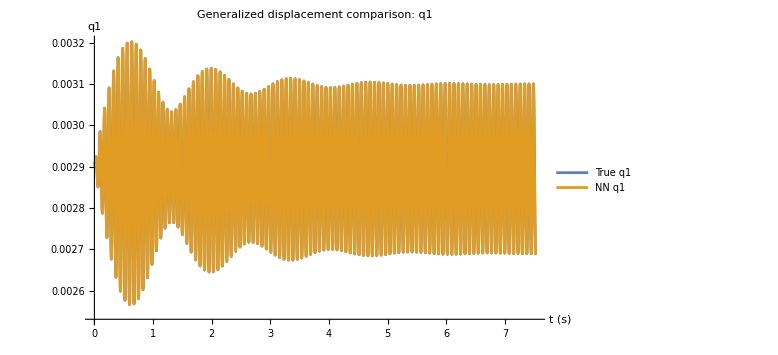

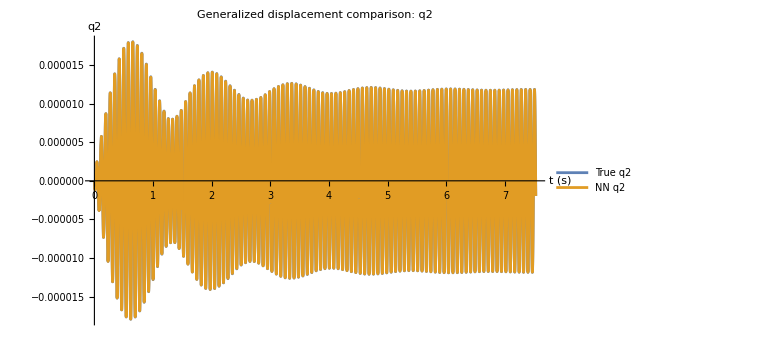

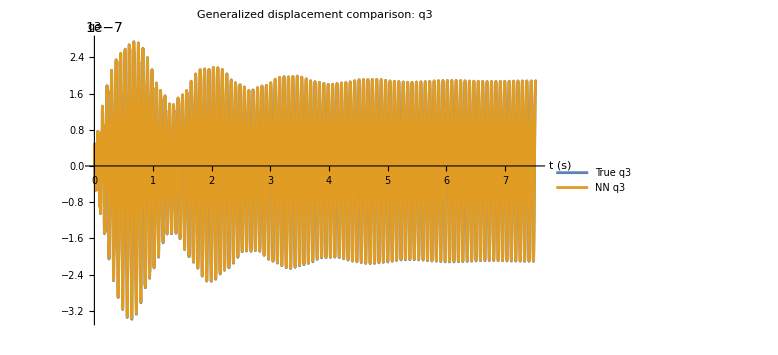

Observation position:

xObs/L = 0.5

mode-shape vector = {1.,1.22465×10^-16,-1.}

Generalized-displacement RMSE:

q1 RMSE = 3.52373×10^-7

q2 RMSE = 1.96228×10^-8

q3 RMSE = 8.30324×10^-10

Midpoint physical-displacement errors:

w(L/2) RMSE = 3.52715×10^-7

w(L/2) MAE = 2.94714×10^-7

w(L/2) MaxAbsError = 8.83269×10^-7

-Graphics-

-Graphics-

-Graphics-

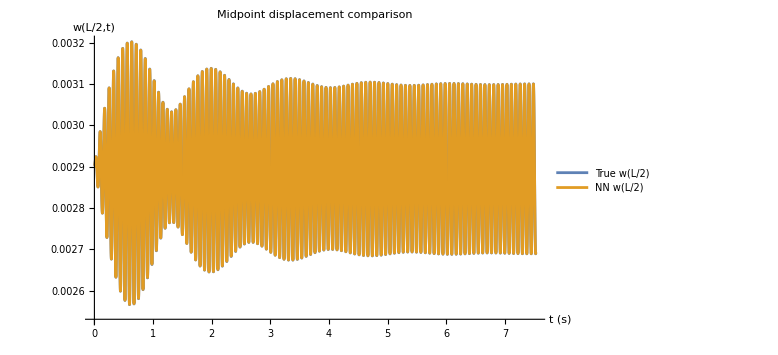

Summary Excel exported:

C:\Users\Lpp\Desktop\data-drivenpipe\code_pipe\pipe_true_NN_error_summary.xlsx

Time-history CSV exported:

C:\Users\Lpp\Desktop\data-drivenpipe\code_pipe\pipe_true_NN_time_history_with_midpoint.csv

Mathematica result exported.

DONE.

```mathematica
(* ::Section::*)(*Pipe true model versus NN:generalized time-history comparison*)ClearAll["Global`*"];

SetDirectory@If[$InputFileName==="",NotebookDirectory[],DirectoryName[$InputFileName]];

Print["Current directory: ",Directory[]];

(* ============================================================*)
(*1. File names*)
(* ============================================================*)

netFile="trainedNet_pipe_flow_cos_final.wlnet";
normFile="normParams_pipe_flow_cos_final.mx";

If[!FileExistsQ[netFile],Print["ERROR: network file not found: ",netFile];
Abort[];];

If[!FileExistsQ[normFile],Print["ERROR: normalization file not found: ",normFile];
Abort[];];

(* ============================================================*)
(*2. Physical parameters from pipe_simple(4).nb*)
(* ============================================================*)

L=1.0;

Douter=0.01;
Dinner=0.009;

EYoung=2.06*10^11;

rhoS=7850.;
rhoF=1000.;

AreaPipe=Pi/4 (Douter^2-Dinner^2);
AreaFluid=Pi/4 Dinner^2;

Isec=Pi/64 (Douter^4-Dinner^4);

mLine=rhoS AreaPipe+rhoF AreaFluid;

T0=0.0;
cDamp=0.3;

Nmodes=3;

(*Simply supported mode functions*)

phi[n_Integer,x_]:=Sin[n Pi x/L];

(* ============================================================*)
(*3. Galerkin matrices*)
(* ============================================================*)

Print["\nBuilding physical-model matrices..."];

Mmat=Table[mLine Integrate[phi[i,x] phi[j,x],{x,0,L}],{i,1,Nmodes},{j,1,Nmodes}];

Kbend=Table[EYoung Isec Integrate[D[phi[i,x],{x,2}] D[phi[j,x],{x,2}],{x,0,L}],{i,1,Nmodes},{j,1,Nmodes}];

KaxInt=Table[Integrate[D[phi[i,x],x] D[phi[j,x],x],{x,0,L}],{i,1,Nmodes},{j,1,Nmodes}];

Gmat=Table[Integrate[phi[i,x] D[phi[j,x],x],{x,0,L}],{i,1,Nmodes},{j,1,Nmodes}];

Jmat=Table[Integrate[phi[i,x] D[phi[j,x],{x,2}],{x,0,L}],{i,1,Nmodes},{j,1,Nmodes}];

Cmat=(cDamp/mLine) Mmat;

(*Convert everything to machine-real numbers*)

Mmat=N[Mmat];
Kbend=N[Kbend];
KaxInt=N[KaxInt];
Gmat=N[Gmat];
Jmat=N[Jmat];
Cmat=N[Cmat];

Print["  Dimensions[Mmat]   = ",Dimensions[Mmat]];
Print["  Dimensions[Kbend]  = ",Dimensions[Kbend]];
Print["  Dimensions[KaxInt] = ",Dimensions[KaxInt]];
Print["  Dimensions[Gmat]   = ",Dimensions[Gmat]];
Print["  Dimensions[Jmat]   = ",Dimensions[Jmat]];

If[!And@@(Dimensions[#]==={Nmodes,Nmodes}&/@{Mmat,Kbend,KaxInt,Gmat,Jmat,Cmat}),Print["ERROR: physical-model matrix dimension is incorrect."];
Abort[];];

If[!ArrayQ[Mmat,2,NumericQ],Print["ERROR: Mmat is not numerical."];
Abort[];];

massSolver=LinearSolve[Mmat];

Print["Physical-model matrices completed."];

(* ============================================================*)
(*4. Load neural network and normalization data*)
(* ============================================================*)

Print["\nLoading neural network..."];

trainedNet=Import[netFile];
normParams=Import[normFile];

inputMean=N[normParams["inputMean"]];
inputStd=N[normParams["inputStd"]];

targetMean=Which[KeyExistsQ[normParams,"targetMean"],N[normParams["targetMean"]],KeyExistsQ[normParams,"targetMeanGa"],N[normParams["targetMeanGa"]],True,Print["ERROR: target mean not found in normParams."];
Abort[]];

targetStd=Which[KeyExistsQ[normParams,"targetStd"],N[normParams["targetStd"]],KeyExistsQ[normParams,"targetStdGa"],N[normParams["targetStdGa"]],True,Print["ERROR: target standard deviation not found in normParams."];
Abort[]];

inputStd=inputStd/. x_/;Abs[x]<10^-14->1.;
targetStd=targetStd/. x_/;Abs[x]<10^-14->1.;

inputDim=Length[inputMean];
outputDim=Length[targetMean];

Print["  NN input dimension  = ",inputDim];
Print["  NN output dimension = ",outputDim];

If[inputDim=!=2+2 Nmodes,Print["ERROR: expected NN input dimension = ",2+2 Nmodes,", but obtained ",inputDim];
Abort[];];

If[outputDim=!=Nmodes,Print["ERROR: expected NN output dimension = ",Nmodes,", but obtained ",outputDim];
Abort[];];

(* ============================================================*)
(*5. Safe normalization*)
(* ============================================================*)

NormalizeInput[x_?VectorQ]:=MapThread[(#1-#2)/#3&,{N[x],inputMean,inputStd}];

DenormalizeTarget[y_?VectorQ]:=MapThread[#1 #3+#2&,{N[y],targetMean,targetStd}];

(* ============================================================*)
(*6. True model acceleration*)
(* ============================================================*)

TrueAcceleration[t_?NumericQ,q_?VectorQ,qd_?VectorQ,U0_?NumericQ,dU_?NumericQ,Omega_?NumericQ]:=Module[{qq,vv,UNow,Ceff,Keff,Sgeo,nonlinearForce,totalForce,qdd},qq=N[q];
vv=N[qd];
UNow=N[U0+dU Cos[Omega t]];
Ceff=Cmat+2 rhoF AreaFluid UNow Gmat;
Keff=Kbend+(T0-rhoF AreaFluid UNow^2) KaxInt;
Sgeo=qq.KaxInt.qq;
nonlinearForce=-(EYoung AreaPipe/(2 L))*Sgeo*(Jmat.qq);
totalForce=Ceff.vv+Keff.qq+nonlinearForce;
qdd=massSolver[-N[totalForce]];
If[!VectorQ[qdd,NumericQ]||Length[qdd]=!=Nmodes,Print["ERROR: true acceleration is not numerical at t = ",t];
Print["  U(t) = ",UNow];
Print["  q = ",qq];
Print["  qd = ",vv];
Print["  totalForce = ",totalForce];
Return[ConstantArray[Indeterminate,Nmodes]]];
N[qdd]];

(* ============================================================*)
(*7. NN acceleration*)
(* ============================================================*)

NNAcceleration[t_?NumericQ,q_?VectorQ,qd_?VectorQ,U0_?NumericQ,dU_?NumericQ,Omega_?NumericQ]:=Module[{dUcos,nnInput,inputNormalized,outputNormalized,qdd},dUcos=N[dU Cos[Omega t]];
nnInput=Join[{N[U0],dUcos},N[q],N[qd]];
If[Length[nnInput]=!=inputDim,Print["ERROR: NN input length = ",Length[nnInput],", expected ",inputDim];
Return[ConstantArray[Indeterminate,Nmodes]]];
inputNormalized=NormalizeInput[nnInput];
outputNormalized=trainedNet[inputNormalized];
qdd=DenormalizeTarget[outputNormalized];
If[!VectorQ[qdd,NumericQ]||Length[qdd]=!=Nmodes,Print["ERROR: NN acceleration is not numerical at t = ",t];
Print["  NN input = ",nnInput];
Print["  normalized input = ",inputNormalized];
Print["  NN output = ",outputNormalized];
Return[ConstantArray[Indeterminate,Nmodes]]];
N[qdd]];

(* ============================================================*)
(*8. Explicit state-space functions*)
(* ============================================================*)

TrueRHS[t_?NumericQ,state_?VectorQ,U0_?NumericQ,dU_?NumericQ,Omega_?NumericQ]:=Module[{q,qd,qdd},q=state[[1;;Nmodes]];
qd=state[[Nmodes+1;;2 Nmodes]];
qdd=TrueAcceleration[t,q,qd,U0,dU,Omega];
Join[qd,qdd]];

NNRHS[t_?NumericQ,state_?VectorQ,U0_?NumericQ,dU_?NumericQ,Omega_?NumericQ]:=Module[{q,qd,qdd},q=state[[1;;Nmodes]];
qd=state[[Nmodes+1;;2 Nmodes]];
qdd=NNAcceleration[t,q,qd,U0,dU,Omega];
Join[qd,qdd]];

(* ============================================================*)
(*9. Fourth-order Runge-Kutta*)
(* ============================================================*)

RK4Step[rhs_,t_?NumericQ,state_?VectorQ,h_?NumericQ,U0_?NumericQ,dU_?NumericQ,Omega_?NumericQ]:=Module[{k1,k2,k3,k4},k1=rhs[t,state,U0,dU,Omega];
k2=rhs[t+h/2,state+h k1/2,U0,dU,Omega];
k3=rhs[t+h/2,state+h k2/2,U0,dU,Omega];
k4=rhs[t+h,state+h k3,U0,dU,Omega];
N[state+h (k1+2 k2+2 k3+k4)/6]];

(* ============================================================*)
(*10. General time-history solver*)
(* ============================================================*)

Options[SimulateSystem]={"PrintEvery"->5000,"DivergenceLimit"->100.};

SimulateSystem[rhs_,U0_?NumericQ,dU_?NumericQ,Omega_?NumericQ,q0_?VectorQ,qd0_?VectorQ,tEnd_?NumericQ,h_?NumericQ,OptionsPattern[]]:=Module[{printEvery,divergenceLimit,nSteps,tList,stateList,stateNow,stateNew,tNow,lastIndex,i},printEvery=OptionValue["PrintEvery"];
divergenceLimit=OptionValue["DivergenceLimit"];
If[Length[q0]=!=Nmodes,Print["ERROR: Length[q0] must be ",Nmodes];
Return[$Failed]];
If[Length[qd0]=!=Nmodes,Print["ERROR: Length[qd0] must be ",Nmodes];
Return[$Failed]];
nSteps=Floor[tEnd/h];
tList=N[Range[0,nSteps] h];
stateList=ConstantArray[0.,{nSteps+1,2 Nmodes}];
stateNow=N@Join[q0,qd0];
stateList[[1]]=stateNow;
lastIndex=1;
Do[tNow=tList[[i]];
stateNew=RK4Step[rhs,tNow,stateNow,h,U0,dU,Omega];
If[!VectorQ[stateNew,NumericQ]||!FreeQ[stateNew,Indeterminate|ComplexInfinity|DirectedInfinity[_]],Print["Integration stopped because a nonnumeric value appeared at t = ",tNow];
Break[];];
If[Max[Abs[stateNew]]>divergenceLimit,Print["Integration stopped because the state exceeded the limit at t = ",tNow];
Break[];];
stateNow=stateNew;
stateList[[i+1]]=stateNow;
lastIndex=i+1;
If[IntegerQ[printEvery]&&printEvery>0&&Mod[i,printEvery]==0,Print["Step ",i,"/",nSteps," | t = ",NumberForm[tNow,{12,6}]," | Max|q| = ",ScientificForm[Max[Abs[stateNow[[1;;Nmodes]]]],4]];];,{i,1,nSteps}];
<|"t"->tList[[1;;lastIndex]],"state"->stateList[[1;;lastIndex]],"q"->stateList[[1;;lastIndex,1;;Nmodes]],"qd"->stateList[[1;;lastIndex,Nmodes+1;;2 Nmodes]]|>];

(* ============================================================*)
(*11. Calculation parameters*)
(* ============================================================*)

(*Flow velocity:U(t)=U0+dU Cos[Omega t] These values follow pipe_simple(4).nb.*)

U0=80.;
dU=0.1;
Omega=13.29*2 Pi;

(*Initial generalized displacement and velocity*)

q0={0.0029,0.,0.};
qd0={0.,0.,0.};

nCycles=100;

(*Use more points per period for the high-frequency model*)

nPerCycle=400;

period=2 Pi/Omega;
tEnd=nCycles period;
h=period/nPerCycle;

Print["\nCalculation settings:"];
Print["  U0       = ",U0];
Print["  dU       = ",dU];
Print["  Omega    = ",Omega];
Print["  frequency = ",Omega/(2 Pi)," Hz"];
Print["  period   = ",period];
Print["  tEnd     = ",tEnd];
Print["  h        = ",h];
Print["  nSteps   = ",Floor[tEnd/h]];

(* ============================================================*)
(*12. Numerical tests at t=0*)
(* ============================================================*)

testState=N@Join[q0,qd0];

testTrueRHS=TrueRHS[0.,testState,U0,dU,Omega];

testNNRHS=NNRHS[0.,testState,U0,dU,Omega];

Print["\nNumerical test at t = 0:"];

Print["  TrueRHS = ",testTrueRHS];
Print["  TrueRHS numerical = ",VectorQ[testTrueRHS,NumericQ]];

Print["  NNRHS = ",testNNRHS];
Print["  NNRHS numerical = ",VectorQ[testNNRHS,NumericQ]];

If[!VectorQ[testTrueRHS,NumericQ]||Length[testTrueRHS]=!=2 Nmodes,Print["ERROR: true model failed the t=0 numerical test."];
Abort[];];

If[!VectorQ[testNNRHS,NumericQ]||Length[testNNRHS]=!=2 Nmodes,Print["ERROR: NN model failed the t=0 numerical test."];
Abort[];];

(* ============================================================*)
(*13. Compute true and NN responses*)
(* ============================================================*)

Print["\nCalculating true-model response..."];

solTrue=SimulateSystem[TrueRHS,U0,dU,Omega,q0,qd0,tEnd,h,"PrintEvery"->5000,"DivergenceLimit"->100.];

Print["\nCalculating NN response..."];

solNN=SimulateSystem[NNRHS,U0,dU,Omega,q0,qd0,tEnd,h,"PrintEvery"->5000,"DivergenceLimit"->100.];

If[solTrue===$Failed||solNN===$Failed,Abort[];];

(* ============================================================*)
(*14. Align time histories*)
(* ============================================================*)

nCompare=Min[Length[solTrue["t"]],Length[solNN["t"]]];

tCompare=solTrue["t"][[1;;nCompare]];

qTrue=solTrue["q"][[1;;nCompare]];
qdTrue=solTrue["qd"][[1;;nCompare]];

qNN=solNN["q"][[1;;nCompare]];
qdNN=solNN["qd"][[1;;nCompare]];

(* ============================================================*)
(*15. Plot only generalized-displacement comparisons*)
(* ============================================================*)

comparisonFigures=Table[ListLinePlot[{Transpose[{tCompare,qTrue[[All,mode]]}],Transpose[{tCompare,qNN[[All,mode]]}]},PlotLegends->{"True q"<>ToString[mode],"NN q"<>ToString[mode]},AxesLabel->{"t (s)","q"<>ToString[mode]},PlotLabel->"Generalized displacement comparison: q"<>ToString[mode],PlotRange->All,ImageSize->Large],{mode,1,Nmodes}];

Print/@comparisonFigures;

(* ============================================================*)(*16. Generalized-coordinate and midpoint-displacement errors*)(* ============================================================*)qError=qNN-qTrue;
qdError=qdNN-qdTrue;

qRMSE=Sqrt[Mean/@Transpose[qError^2]];

qdRMSE=Sqrt[Mean/@Transpose[qdError^2]];

qMAE=Mean/@Transpose[Abs[qError]];
qdMAE=Mean/@Transpose[Abs[qdError]];

qMaxAbsError=Max/@Transpose[Abs[qError]];
qdMaxAbsError=Max/@Transpose[Abs[qdError]];

(*------------------------------------------------------------*)
(*Physical displacement at x=L/2*)
(*------------------------------------------------------------*)

xObs=L/2;

modeShapeAtObs=Table[Sin[mode Pi xObs/L],{mode,1,Nmodes}];

Print["\nObservation position:"];
Print["  xObs/L = ",xObs/L];
Print["  mode-shape vector = ",modeShapeAtObs];

wTrue=qTrue.modeShapeAtObs;
wNN=qNN.modeShapeAtObs;
wError=wNN-wTrue;

wdTrue=qdTrue.modeShapeAtObs;
wdNN=qdNN.modeShapeAtObs;
wdError=wdNN-wdTrue;

wRMSE=Sqrt[Mean[wError^2]];
wMAE=Mean[Abs[wError]];
wMaxAbsError=Max[Abs[wError]];

wdRMSE=Sqrt[Mean[wdError^2]];
wdMAE=Mean[Abs[wdError]];
wdMaxAbsError=Max[Abs[wdError]];

Print["\nGeneralized-displacement RMSE:"];

Do[Print["  q",mode," RMSE = ",ScientificForm[qRMSE[[mode]],6]],{mode,1,Nmodes}];

Print["\nMidpoint physical-displacement errors:"];

Print["  w(L/2) RMSE = ",ScientificForm[wRMSE,6]];

Print["  w(L/2) MAE = ",ScientificForm[wMAE,6]];

Print["  w(L/2) MaxAbsError = ",ScientificForm[wMaxAbsError,6]];

(* ============================================================*)
(*17. Plot only displacement comparisons*)
(* ============================================================*)

comparisonFigures=Table[ListLinePlot[{Transpose[{tCompare,qTrue[[All,mode]]}],Transpose[{tCompare,qNN[[All,mode]]}]},PlotLegends->{"True q"<>ToString[mode],"NN q"<>ToString[mode]},AxesLabel->{"t (s)","q"<>ToString[mode]},PlotLabel->"Generalized displacement comparison: q"<>ToString[mode],PlotRange->All,ImageSize->Large],{mode,1,Nmodes}];

Print/@comparisonFigures;

figWMidCompare=ListLinePlot[{Transpose[{tCompare,wTrue}],Transpose[{tCompare,wNN}]},PlotLegends->{"True w(L/2)","NN w(L/2)"},AxesLabel->{"t (s)","w(L/2,t)"},PlotLabel->"Midpoint displacement comparison",PlotRange->All,ImageSize->Large];

Print[figWMidCompare];

(* ============================================================*)
(*18. Prepare export data*)
(* ============================================================*)

displacementHeader=Flatten[Table[{"q"<>ToString[mode]<>"_True","q"<>ToString[mode]<>"_NN","q"<>ToString[mode]<>"_Error"},{mode,1,Nmodes}]];

velocityHeader=Flatten[Table[{"qd"<>ToString[mode]<>"_True","qd"<>ToString[mode]<>"_NN","qd"<>ToString[mode]<>"_Error"},{mode,1,Nmodes}]];

excelHeader=Join[{"t"},displacementHeader,velocityHeader,{"w_L2_True","w_L2_NN","w_L2_Error","wd_L2_True","wd_L2_NN","wd_L2_Error"}];

excelData=Table[Join[{tCompare[[i]]},Flatten[Table[{qTrue[[i,mode]],qNN[[i,mode]],qError[[i,mode]]},{mode,1,Nmodes}]],Flatten[Table[{qdTrue[[i,mode]],qdNN[[i,mode]],qdError[[i,mode]]},{mode,1,Nmodes}]],{wTrue[[i]],wNN[[i]],wError[[i]],wdTrue[[i]],wdNN[[i]],wdError[[i]]}],{i,1,nCompare}];

summaryData=Join[{{"Parameter","Value"},{"U0",U0},{"dU",dU},{"Omega",Omega},{"Frequency_Hz",Omega/(2 Pi)},{"Period",period},{"TimeStep",h},{"NumberOfCycles",nCycles},{"NumberOfModes",Nmodes},{"ObservationPosition",xObs},{"ObservationPositionOverL",xObs/L}},Flatten[Table[{{"q"<>ToString[mode]<>"_RMSE",qRMSE[[mode]]},{"q"<>ToString[mode]<>"_MAE",qMAE[[mode]]},{"q"<>ToString[mode]<>"_MaxAbsError",qMaxAbsError[[mode]]},{"qd"<>ToString[mode]<>"_RMSE",qdRMSE[[mode]]},{"qd"<>ToString[mode]<>"_MAE",qdMAE[[mode]]},{"qd"<>ToString[mode]<>"_MaxAbsError",qdMaxAbsError[[mode]]}},{mode,1,Nmodes}],1],{{"w_L2_RMSE",wRMSE},{"w_L2_MAE",wMAE},{"w_L2_MaxAbsError",wMaxAbsError},{"wd_L2_RMSE",wdRMSE},{"wd_L2_MAE",wdMAE},{"wd_L2_MaxAbsError",wdMaxAbsError}}];

(* ============================================================*)
(*19. Export*)
(* ============================================================*)

summaryExcelFile="pipe_true_NN_error_summary.xlsx";

timeHistoryCSVFile="pipe_true_NN_time_history_with_midpoint.csv";

Export[summaryExcelFile,{"Summary"->summaryData},"XLSX"];

Export[timeHistoryCSVFile,Prepend[excelData,excelHeader],"CSV"];

Print["\nSummary Excel exported:"];

Print["  ",FileNameJoin[{Directory[],summaryExcelFile}]];

Print["Time-history CSV exported:"];

Print["  ",FileNameJoin[{Directory[],timeHistoryCSVFile}]];

(* ============================================================*)
(*20. Save complete Mathematica result*)
(* ============================================================*)

resultPack=<|"U0"->U0,"dU"->dU,"Omega"->Omega,"q0"->q0,"qd0"->qd0,"t"->tCompare,"qTrue"->qTrue,"qNN"->qNN,"qError"->qError,"qdTrue"->qdTrue,"qdNN"->qdNN,"qdError"->qdError,"qRMSE"->qRMSE,"qMAE"->qMAE,"qMaxAbsError"->qMaxAbsError,"qdRMSE"->qdRMSE,"qdMAE"->qdMAE,"qdMaxAbsError"->qdMaxAbsError,"xObs"->xObs,"modeShapeAtObs"->modeShapeAtObs,"wTrue"->wTrue,"wNN"->wNN,"wError"->wError,"wdTrue"->wdTrue,"wdNN"->wdNN,"wdError"->wdError,"wRMSE"->wRMSE,"wMAE"->wMAE,"wMaxAbsError"->wMaxAbsError,"wdRMSE"->wdRMSE,"wdMAE"->wdMAE,"wdMaxAbsError"->wdMaxAbsError,"netFile"->netFile,"normFile"->normFile|>;

Export["pipe_true_NN_time_history_result.mx",resultPack,"MX"];

Print["Mathematica result exported."];
Print["DONE."];
```